```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\NumericalIntegration.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\Heston_Definitif.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_VanillaInstruments.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_Calibration.m"
```

```mathematica
process
```

Le process est :

dS_t/S_t=α_S √(v_(1,t)) dW_(1,t)+β_S √(v_(2,t)) dW_(2,t);
dv_(1,t)=λ_1(θ_1-v_(1,t))dt+κ_1 √(v_(1,t)) d(W̄)_(1,t);
dv_(2,t)=λ_2(θ_2-v_(2,t))dt+κ_2 √(v_(2,t)) d(W̄)_(2,t)
 dW_(1,t)d(W̄)_(1,t)=ρ_1 dt;
 dW_(2,t)d(W̄)_(2,t)=ρ_2 dt

```mathematica
ici Subscript[α, S] et Subscript[β, S] jouent  le role de valeur initiale de V
```

```mathematica
Soit Subscript[X, t]=Log[Subscript[S, t]]
```

```mathematica
on obtient le process
```

```mathematica
Subscript[dX, t]=-1/2(Subscript[α, 1]^2 Subscript[v, 1,t]+Subscript[β, 1]^2 Subscript[v, 2,t])dt+Subscript[α, 1] √Subscript[v, 1,t] Subscript[dW, 1,t]+Subscript[β, 1] √Subscript[v, 2,t] Subscript[dW, 2,t];  avec Subscript[X, 0]=Log[Subscript[S, 0]]
```

```mathematica
Transformée fondamentale
```

{-(∂ P)/(∂t)=(α_1^2 V_1+β_1^2 V_2)/2(∂^2 P)/(∂x^2)+(κ_1^2 V_1)/2(∂^2 P)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 P)/(∂V_2^2)+ρ_1 κ_1  v_1 α_1(∂^2 P)/(∂V_1 ∂x)+ρ_2 κ_2  v_2 β_1(∂^2 P)/(∂V_2 ∂S)+ λ_1(θ_1-v_1)(∂ P)/(∂V_1)+λ_2(θ_2-v_2)(∂ P)/(∂V_2)-1/2(α_1^2 v_1+β_1^2 v_2)(∂ P)/(∂x)
P(0)=(ⅇ^x-K)^+

```mathematica
soit q la transformé de fourier par rapport a S
```

q[z]=∫_(-∞)^∞ ⅇ^(ⅈ z  x)P[x]ⅆx

∫_(-∞)^∞ ⅇ^(ⅈ z  x)(∂ P)/(∂x)ⅆx=([ⅇ^(ⅈ z  x)P]^∞)_(-∞)-∫_(-∞)^∞ ⅈ Z ⅇ^(ⅈ z x)Pⅆx=∫_(-∞)^∞ (-ⅈ Z )ⅇ^(ⅈ z  x)Pⅆx

τ = T - t

{(∂ q)/(∂τ)=-(V_1+V_2)/2 Z^2 q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)-ⅈ Z ρ_1 κ_1  v_1(∂ q)/(∂V_1)-ⅈ Z ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)+(ⅈ Z)/2(v_1+v_2)q
q(0)=∫_(-∞)^∞ ⅇ^(ⅈ ω x)(ⅇ^x-K)^+ⅆx

```mathematica
soit
```

{(∂ q)/(∂τ)=(V_1+V_2)/2(ⅈ Z-Z^2)q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)-ⅈ Z ρ_1 κ_1  v_1(∂ q)/(∂V_1)-ⅈ Z ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)
q(0)=∫_(-∞)^∞ ⅇ^(ⅈ ω x)(ⅇ^x-K)^+ⅆx

```mathematica
Solve[α ⅇ^(a x)-K==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[K/α]/a}}

```mathematica
Simplify[∫_(Log[K/α]/a)^∞ ⅇ^(ⅈ k  x)(α ⅇ^(a x)-K)ⅆx]
```

If[Im[k]>0&&Re[a]<Im[k],(a K (K/α)^((ⅈ k)/a))/(ⅈ a k-k^2),Integrate[-ⅇ^(ⅈ k x) K+ⅇ^(a x+ⅈ k x) α,{x,Log[K/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k]≤0)||(Re[a]>0&&Im[k]≤Re[a])]]

donc q(ω,V_1,V_2,0)=(a K (K/α)^((ⅈ k)/a))/(ⅈ a k-k^2)≡q_0(ω)

donc on definit

q[Z,V_1,V_2,t]=q_1[Z,V_1,V_2,t]q_0[Z]

{(∂ q_1)/(∂τ)=(V_1+V_2)/2(ⅈ Z-Z^2)q_1+(κ_1^2 V_1)/2(∂^2 q_1)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q_1)/(∂V_2^2)-ⅈ Z ρ_1 κ_1  v_1(∂ q_1)/(∂V_1)-ⅈ Z ρ_2 κ_2  v_2(∂ q_1)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q_1)/(∂V_1)+λ_2(θ_2-v_2)(∂ q_1)/(∂V_2)
q_1(0)=1

ce qui nous permet de nous debarasser a la fois d' une dimension et de la dependance  vis a vis de la condition aux limite

Call=1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])q_1[Z,V_1,V_2,t]q_0[Z]ⅆZ=-1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])(a K (K/α)^((ⅈ k)/a))/(ⅈ a k-k^2)q_1[Z,V_1,V_2,t]ⅆZ

```mathematica
ou Subscript[z, i] > 1
```

On fait ensuite l' hypothese affine

q_1[V_1,V_2,τ]=ⅇ^(A[τ]+B_1[τ] V_1+B_2[τ] V_2)

```mathematica
afin de resoudre l'equation differentielle qui nous reste
```

then we have( (∂A[τ])/(∂τ)+(∂B_1[τ])/(∂τ) V_1+(∂B_2[τ])/(∂τ) V_2)q_1=((κ_1^2 V_1)/2 B_1[τ]^2+(κ_2^2 V_2)/2 B_2[τ]^2+(λ_1 θ_1-V_1 ( λ_1+ⅈ ρ_1 Z κ_1))B_1[τ]+(λ_2 θ_2-V_2 ( λ_12+ⅈ ρ_2 Z κ_2))B_2[τ]-((V_1+V_2) (Z^2-ⅈ Z))/2)q_1

en identifiant les termes homogene a V_1, puis V_2, puis les termes de degres 0 on obtient les equations

{(∂A[τ])/(∂τ)=λ_1 θ_1 B_1[τ]+λ_2 θ_2 B_2[τ]
(∂B_1[τ])/(∂τ)=κ_1^2/2 B_1[τ]^2- ( λ_1+ⅈ ρ_1 Z κ_1)B_1[τ]-(Z^2-ⅈ Z)/2
(∂B_2[τ])/(∂τ)=κ_2^2/2 B_2[τ]^2- ( λ_2+ⅈ ρ_2 Z κ_2)B_2[τ]-(Z^2-ⅈ Z)/2

```mathematica
comme Subscript[q, 1](0)=1 on a les conditions initiales:Subscript[B, 1][0]=Subscript[B, 2][0]=A[0]=0
```

Calcul de B_i[τ]

nous allons resoudre le systeme ou B_i[0]=B_(i,0)    pour le cas ou on a une time dependence (constant par morceaux)

df/dτ=a f^2+b f+c

with

{a=κ^2/2
b=- ( λ+ⅈ ρ  ω κ)
c=-(ω^2-ⅈ ω)/2

So we compute the discriminant:Δ=b^2-4a c=( λ+ⅈ ρ ω κ)^2+ κ^2   (ω^2-ⅈ ω)

let ζ=√Δ

{x_1= (( λ+ⅈ ρ ω κ)-ζ)/κ^2
x_2= (( λ+ⅈ ρ ω κ)+ζ)/κ^2

on a bien sur : x_1 x_2=c/a=(-(ω^2-ⅈ ω))/κ^2  et   x_1+x_2=-b/a=2( λ+ⅈ ρ  ωκ)/κ^2  et   x1-x2=(-2ζ)/κ^2

donc   df/(( f-x1)(f-x2))=a dτ  et  1/( f-x1)-1/(f-x2)=(( f-x2)-( f-x1))/(( f-x1)(f-x2))=( x1-x2)/(( f-x1)(f-x2))

et      df (1/( f-x1)-1/(f-x2))=a (x1-x2)dτ

```mathematica
mais  a (x1-x2)=κ^2/2(-2ζ)/κ^2=-ζ
```

donc  Log[(B[τ]-x_1)/(B[τ]-x_2)]=-ζ τ+C  et   B[τ]-x_1=ⅇ^(-ζ  τ+C)(B[τ]-x_2)

donc

B[τ]=(x_1-ⅇ^(-ζ  τ+C)x_2)/(1-ⅇ^(-ζ  τ+C))

We determine C by :  B[0]=0 ⟺  x_1-ⅇ^C x_2=0  So  ⅇ^C(-x_2)=-x_1

ⅇ^C=x_1/x_2

donc B[τ]=(x_1-ⅇ^(-ζ  τ)x_1)/(1-ⅇ^(-ζ  τ)x_1/x_2)=(x_1 x_2(1-ⅇ^(-ζ  τ)))/(x_2-x_1 ⅇ^(-ζ  τ))=((-(ω^2-ⅈ ω))/κ^2(1-ⅇ^(-ζ  τ)))/(x_2-x_1 ⅇ^(-ζ  τ))

we create

ψp = -(λ + ρ κ  ⅈ ω) + ζ= -x_1 κ^2   et   ψm = (λ + ρ κ  ⅈ ω) + ζ=  x_2 κ^2

donc x_1=-ψp/κ^2  et x_2=ψm/κ^2   ainsi que ψp +ψm =2 ζ

```mathematica
et   B[τ]=((-(ω^2-ⅈ ω))/κ^2(1-ⅇ^(-ζ  τ)))/(ψm/κ^2--ψp/κ^2 ⅇ^(-ζ  τ))=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ))
```

B[τ]=(-(1-ⅇ^(-ζ  τ)) (ω^2-ⅈ ω))/(ⅇ^(-ζ  τ)ψp+ψm)

on en deduit donc les equations :

B_1[τ]=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ_1  τ)))/(ψm_1+ψp_1 ⅇ^(-ζ_1  τ)); ζ_1=√(( λ_1+ⅈ ρ_1 ω κ_1)^2+ κ_1^2   (ω^2-ⅈ ω));ψp_1 =-(λ_1+ρ_1 κ_1  ⅈ ω)+ζ_1;ψm_1 =(λ_1+ρ_1 κ_1  ⅈ ω)+ζ_1;

B_2[τ]=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ_2  τ)))/(ψm_2+ψp_2 ⅇ^(-ζ_2  τ)); ζ_2=√(( λ_2+ⅈ ρ_2 ω κ_2)^2+ κ_2^2   (ω^2-ⅈ ω));ψp_2 =-(λ_2+ρ_2 κ_2  ⅈ ω)+ζ_2;ψm_1 =(λ_2+ρ_2 κ_2  ⅈ ω)+ζ_2;

maintenant on exploite : (∂A[τ])/(∂τ)=λ_1 θ_1 B_1[τ]+λ_2 θ_2 B_2[τ]        avec A[0]=0

```mathematica
Simplify[Integrate[(-(1-ⅇ^(-ζ  t)) (ω^2-ⅈ ω))/(ⅇ^(-ζ  t)ψp+ψm),{t,0,τ}] ]
```

(ω (-ⅈ+ω) (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

```mathematica
c'est a dire :
```

```mathematica
(ω (-ⅈ+ω) (ζ τ ψm+2ζ Log[(2ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ζ ψm ψp)
```

```mathematica
(θ λ ω^2 (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp) /.{ ψp+ψm->2ζ,ψp ψm->κ^2   ω^2}
```

(θ λ ω^2 (ζ τ ψm+2 ζ Log[2 ζ]-2 ζ Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

donc

A[τ]=θ_1 λ_1 (τ (ω^2-ⅈ ω)ζ_1 ψm_1+(Log[(2 ζ_1)/(ⅇ^(ζ_1 τ) ψm_1+ψp_1)]) (2 ζ_1 ω^2-κ_1^2 2 ζ_1 B_(0,1)^2))/(ψp_1 ζ_1 ψm_1)+θ_2 λ_2 (τ (ω^2-ⅈ ω)ζ_2 ψm_2+(Log[(2 ζ_2)/(ⅇ^(ζ_2 τ) ψm_2+ψp_2)]) (2 ζ_2 ω^2-κ_2^2 2 ζ_2 B_(0,2)^2))/(ψp_2 ζ_2 ψm_2)+ A_0

```mathematica
LNHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,B1,argζ1,ζ2,ψp2 ,ψm2,A2,B2,argζ2,A},
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2( ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ ω)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ ω)+ζ1;
B1=(-( ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ ω)^2+κ2^2( ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ ω)+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ ω)+ζ2;
B2=(-( ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2;
If[Re[A+B1 V1+B2 V2]<-100,0,
ⅇ^(A+B1 V1+B2 V2)]
]
```

```mathematica
Instrument
```

```mathematica
∫_Log[K/S0]^∞ ⅇ^(ⅈ ω S)(ⅇ^(S+Log[S0])-K)ⅆS
```

If[Im[ω]>1,-(K (K/S0)^(ⅈ ω))/(ω (-ⅈ+ω)),Integrate[-ⅇ^(ⅈ S ω) K+ⅇ^(S+ⅈ S ω) S0,{S,Log[K/S0],∞},Assumptions→Im[ω]≤1]]

```mathematica
(ⅈ ⅇ^(ⅈ( K-Log[S0]) ω) (-ⅇ^K Z+K (-ⅈ+Z)))/(Z (-ⅈ+Z))
```

```mathematica
Solve[α ⅇ^(a x)-K==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[K/α]/a}}

```mathematica
integration1=Simplify[∫_(Log[K/α]/a)^∞ ⅇ^(ⅈ k  x)(α ⅇ^(a x)-K)ⅆx]
```

If[Im[k]>0&&Re[a]<Im[k],(a K (K/α)^((ⅈ k)/a))/(ⅈ a k-k^2),Integrate[-ⅇ^(ⅈ k x) K+ⅇ^(a x+ⅈ k x) α,{x,Log[K/α]/a,∞},Assumptions→(Re[a]≤0&&Im[k]≤0)||(Re[a]>0&&Im[k]≤Re[a])]]

```mathematica
integration11=Simplify[integration1,Im[k]>0&&Re[a]<Im[k]]
```

(a K (K/α)^((ⅈ k)/a))/(ⅈ a k-k^2)

```mathematica
en supposant λB>a
```

```mathematica
FourierPayOff[ω_,K_,α_,a_]:=(a K (K/α)^((ⅈ ω)/a))/(ω^2-ⅈ a ω)
```

```mathematica
LNHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) LNHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]FourierPayOff[ω,K,α,a]]
```

```mathematica
SuperHestonVanillaOptionQ[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_]:=S0-1/π Module[{ω},NIntegrate[LNHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2],
{ω,0,Infinity},MaxRecursion->12]]
```

```mathematica
SuperHestonVanillaOption[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_]:=S0-1/π Module[{ω},AdaptativeIntegrate[Function[ω,LNHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2]],LegendreCoeffs[60],LegendreCoeffs[8],30,5,10^(-9),30]][[2]]
```

```mathematica
SuperHestonVanillaOption2[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_]:=S0-1/π Module[{ω},CoeffBasedIntegrate[Function[ω,LNHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2]],LegendreCoeffs[60,0,30]]]
```

```mathematica
Timing[Module[{ρ1=-0.5,ρ2=-0.5,λv1=0.15,κ1=0.2,λv2=0.15,κ2=0.2,k=0.06,V1,V2,Vinfini1,Vinfini2
,T=3,λB=1.1,S0=0.05,α=1,a=1},Vinfini1=0.02;V1=Vinfini1;Vinfini2=0.02;V2=Vinfini2;
{SuperHestonVanillaOptionQ[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,k,α,a,T],
SuperHestonVanillaOption[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,k,α,a,T],
SuperHestonVanillaOption2[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,k,α,a,T]
}]]
```

{5.141,{0.00238126,0.00238126,0.00238126}}

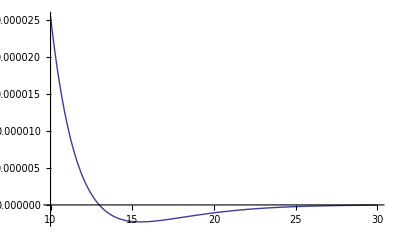
{0.141,-Graphics-}

```mathematica
Timing[Module[{ρ1=-0.5,ρ2=-0.5,λv1=0.15,κ1=0.2,λv2=0.15,κ2=0.2,k=-0.01,V1,V2,Vinfini1,Vinfini2
,T=3,λB=1.1,S0=0.05,α=1,a=1,K=0.05},Vinfini1=0.02;V1=Vinfini1;Vinfini2=0.02;V2=Vinfini2;Plot[
LNHestonCallIntegrand[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2],{ω,10,30},PlotRange->All]]]
```

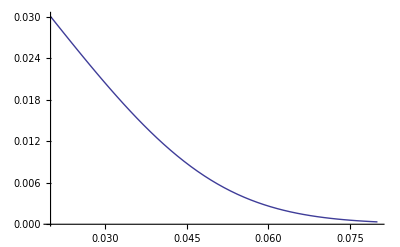
{400.454,-Graphics-}

```mathematica
Timing[Module[{ρ1=-0.5,ρ2=-0.5,λv1=0.15,κ1=0.2,λv2=0.15,κ2=0.2,k=-0.01,V1,V2,Vinfini1,Vinfini2
,T=1,λB=1.1,S0=0.05,α=1,a=1},Vinfini1=0.05;V1=Vinfini1;Vinfini2=0.05;V2=Vinfini2;;Plot[
Re[SuperHestonVanillaOption[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,k,α,a,T]],
{k,0.02,0.08},PlotRange->All]]]
```

```mathematica
Timing[Module[{ρ1=-0.5,ρ2=-0.5,λv1=0.15,κ1=0.2,λv2=0.15,κ2=0.2,k=-0.01,V1,V2,Vinfini1,Vinfini2
,T=3,λB=1.1,S0=0.05,α=1,a=1,K=0.05},Vinfini1=0.02;V1=Vinfini1;Vinfini2=0.02;V2=Vinfini2;Plot[
LNHestonCallIntegrand[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2],{ω,0,1},PlotRange->All]]]
```

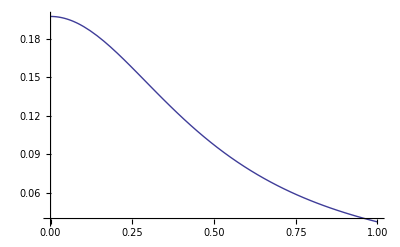
{0.062,-Graphics-}

```mathematica
Timing[Module[{ρ1=-0.5,ρ2=-0.5,λv1=0.15,κ1=0.2,λv2=0.15,κ2=0.2,k=-0.01,V1,V2,Vinfini1,Vinfini2
,T=3,λB=1.1,S0=0.05,α=1,a=1,K=0.05},Vinfini1=0.02;V1=Vinfini1;Vinfini2=0.02;V2=Vinfini2;Plot[
LNHestonCallIntegrand[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,K,α,a,T,ω+ⅈ/2],{ω,0,1},PlotRange->All]]]
```

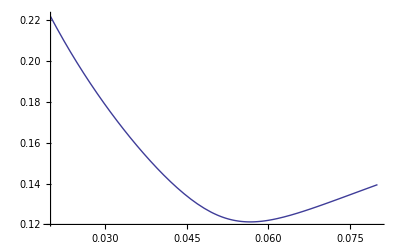
{11.203,-Graphics-}

```mathematica
Timing[Module[{ρ1=-0.2,ρ2=-0.5,λv1=0.35,κ1=0.7,λv2=0.15,κ2=0.5,k=-0.01,V1,V2,Vinfini1,Vinfini2
,T=10,λB=1.1,S0=0.05,α=1,a=1},Vinfini1=0.02;V1=Vinfini1;Vinfini2=0.02;V2=Vinfini2;Plot[
ImpVolBS[S0,k,T,SuperHestonVanillaOption[ρ1,λv1,Vinfini1,κ1,V1,ρ2,λv2,Vinfini2,κ2,V2,S0,k,α,a,T]],
{k,0.02,0.08},PlotRange->All]]]
```

```mathematica
Bi Superheston
```

Variance Process

(dS_(1,t))/(S_(1,t))=α_2 √(v_(2,t)) dW_(2,t)+√(v_(1,t)) dW_(1,t);
(dS_(2,t))/(S_(2,t))=β_2 √(v_(2,t)) dW_(2,t)+√(v_(3,t)) dW_(3,t);
dv_(1,t)=λ_1(θ_1-v_(1,t))dt+κ_1 √(v_(1,t)) d(W̄)_(1,t);
dv_(2,t)=λ_2(θ_2-v_(2,t))dt+κ_2 √(v_(2,t)) d(W̄)_(2,t);
dv_(3,t)=λ_3(θ_3-v_(3,t))dt+κ_3 √(v_(3,t)) d(W̄)_(3,t)
 dW_(1,t)d(W̄)_(1,t)=ρ_1 dt;dW_(2,t)d(W̄)_(2,t)=ρ_2 dt; dW_(3,t)d(W̄)_(3,t)=ρ_3 dt

On montre que

<(dS_(1,t))/(S_(1,t)),(dS_(1,t))/(S_(1,t))> =(α_1^2 v_(1,t)+β_1^2 v_(2,t))dt

<(dS_(2,t))/(S_(2,t)),(dS_(2,t))/(S_(2,t))> =(β_2^2 v_(2,t)+α_2^2 v_(3,t))dt

<(dS_(1,t))/(S_(1,t)),(dS_(2,t))/(S_(2,t))> =α_1 α_2 v_(2,t)dt

```mathematica
Σ=({{v1, 0, 0}, {0, v2, 0}, {0, 0, v3}});Q=({{κ1, 0, 0}, {0, κ2, 0}, {0, 0, κ3}});M=({{λ1, 0, 0}, {0, λ2, 0}, {0, 0, λ3}})
```

```mathematica
Subscript[x, 1,t]=Log[Subscript[S, 1,t]]; Subscript[x, 2,t]=Log[Subscript[S, 2,t]]
```

```mathematica
processus:
```

```mathematica
l'etat : ({{Subscript[x, 1,t]}, {Subscript[x, 2,t]}, {Subscript[v, 1,t]}, {Subscript[v, 2,t]}, {Subscript[v, 3,t]}})  a pour covariance matrice: ({{{{Subscript[v, 1,t]+Subscript[α, 2]^2 Subscript[v, 2,t]}, {Subscript[α, 2] Subscript[β, 2] Subscript[v, 2,t]}, {κ1 ρ1 Subscript[v, 1,t]}, {Subscript[α, 2] κ2 ρ2 Subscript[v, 2,t]}, {0}}, {{Subscript[α, 2] Subscript[β, 2] Subscript[v, 2,t]}, {Subscript[β, 2]^2 Subscript[v, 2,t]+Subscript[v, 3,t]}, {0}, {Subscript[β, 2] κ2ρ2 Subscript[v, 2,t]}, {κ3 ρ3 Subscript[v, 3,t]}}, {{κ1 ρ1 Subscript[v, 1,t]}, {0}, {κ1^2 Subscript[v, 1,t]}, {0}, {0}}, {{Subscript[α, 2] κ2 ρ2 Subscript[v, 2,t]}, {Subscript[β, 2] κ2 ρ2 Subscript[v, 2,t]}, {0}, {κ2^2 Subscript[v, 2,t]}, {0}}, {{0}, {κ3 ρ3 Subscript[v, 3,t]}, {0}, {0}, {κ3^2 Subscript[v, 3,t]}}}}) et pour drift ({{-1/2(Subscript[v, 1,t]+Subscript[v, 2,t])}, {-1/2(Subscript[v, 2,t]+Subscript[v, 3,t])}, {Subscript[λ, 1](Subscript[θ, 1]-Subscript[v, 1,t])}, {Subscript[λ, 2](Subscript[θ, 2]-Subscript[v, 2,t])}, {Subscript[λ, 3](Subscript[θ, 3]-Subscript[v, 3,t])}})
```

```mathematica
c'est donc bien un processus affine et la probabilité de transition est donc de la forme:
```

```mathematica
Exp[ A1  v1 + A2 v2 +A3 v3+ γ1 x1 +γ2 x2  + c]
```

```mathematica
Transformée fondamentale
```

{-(∂ P)/(∂t)=(V_1+α_2^2 V_2)/2(∂^2 P)/(∂x^2)+(κ_1^2 V_1)/2(∂^2 P)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 P)/(∂V_2^2)+ρ_1 κ_1  v_1(∂^2 P)/(∂V_1 ∂x)+α_2 ρ_2 κ_2  v_2(∂^2 P)/(∂V_2 ∂x)+ λ_1(θ_1-v_1)(∂ P)/(∂V_1)+λ_2(θ_2-v_2)(∂ P)/(∂V_2)-1/2(v_1+α_2^2 v_2)(∂ P)/(∂x)+
(β_2^2 V_2+V_3)/2(∂^2 P)/(∂y^2)+(κ_3^2 V_3)/2(∂^2 P)/(∂V_3^2)+ρ_3 κ_3  v_3(∂^2 P)/(∂V_3 ∂y)+β_2 ρ_2 κ_2  v_2(∂^2 P)/(∂V_2 ∂y)+ λ_3(θ_3-v_3)(∂ P)/(∂V_3)+λ_2(θ_2-v_2)(∂ P)/(∂V_2)-1/2(v_3+β_2^2 v_2)(∂ P)/(∂y)+
α_2 β_2 V_2(∂^2 P)/(∂x ∂y)
P(0)=(ⅇ^x-ⅇ^y-K)^+

```mathematica
soit q la transformé de fourier par rapport a   x et y
```

q[z]=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)P[x,y]ⅆx

∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(∂ P)/(∂x)ⅆx=([ⅇ^(ⅈ z1  x+ⅈ z2  y)P]^∞)_(-∞)-∫_(-∞)^∞ ⅈ Z ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx=∫_(-∞)^∞ (-ⅈ Z1 )ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx

```mathematica
∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(∂ P)/(∂y)ⅆx=∫_(-∞)^∞ (-ⅈ Z2 )ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx
```

τ = T - t

{(∂ q)/(∂τ)=-(V_1+α_2^2 V_2)/2 Z1^2 q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)-ⅈ Z1 ρ_1 κ_1  v_1(∂ q)/(∂V_1)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)+(ⅈ Z1)/2(v_1+α_2^2 v_2)q+
-(β_2^2 V_2+V_3)/2 Z2^2 q+(κ_3^2 V_3)/2(∂^2 q)/(∂V_3^2)-ⅈ Z2 ρ_3 κ_3  v_3(∂ q)/(∂V_3)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_3(θ_3-v_3)(∂ q)/(∂V_13)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)+(ⅈ Z2)/2(v_3+β_2^2 v_2)q+
-α_2 β_2 V_2 Z1 Z2 q

q(0)=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(ⅇ^x-ⅇ^y-K)^+ⅆxⅆy

```mathematica
soit
```

{(∂ q)/(∂τ)=(V_1+α_2^2 V_2)/2(ⅈ Z1-Z1^2)q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)-ⅈ Z1 ρ_1 κ_1  v_1(∂ q)/(∂V_1)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)+
(β_2^2 V_2+V_3)/2(ⅈ Z2-Z2^2)q+(κ_3^2 V_3)/2(∂^2 q)/(∂V_3^2)-ⅈ Z2 ρ_3 κ_3  v_3(∂ q)/(∂V_3)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)+ λ_3(θ_3-v_3)(∂ q)/(∂V_3)+λ_2(θ_2-v_2)(∂ q)/(∂V_2)+
-α_2 β_2 V_2 Z1 Z2 q

q(0)=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(ⅇ^x-ⅇ^y-K)^+ⅆxⅆy

```mathematica
on poose
q[Z1,Z2,Subscript[V, 1],Subscript[V, 2],t]=Subscript[q, 1][Z1,Z2,Subscript[V, 1],Subscript[V, 2],t]Subscript[q, 0][Z1,Z2]
```

```mathematica
ou
```

```mathematica
Subscript[q, 0][Z1,Z2]=q(0)
```

```mathematica
alors
```

{(∂ q_1)/(∂τ)=(V_1+α_2^2 V_2)/2(ⅈ Z1-Z1^2)q_1+(κ_1^2 V_1)/2(∂^2 q_1)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q_1)/(∂V_2^2)-ⅈ Z1 ρ_1 κ_1  v_1(∂ q_1)/(∂V_1)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q_1)/(∂V_2)+ λ_1(θ_1-v_1)(∂ q_1)/(∂V_1)+λ_2(θ_2-v_2)(∂ q_1)/(∂V_2)+
(β_2^2 V_2+V_3)/2(ⅈ Z2-Z2^2)q_1+(κ_3^2 V_3)/2(∂^2 q_1)/(∂V_3^2)-ⅈ Z2 ρ_3 κ_3  v_3(∂ q_1)/(∂V_3)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q_1)/(∂V_2)+ λ_3(θ_3-v_3)(∂ q_1)/(∂V_3)+λ_2(θ_2-v_2)(∂ q_1)/(∂V_2)+
-α_2 β_2 V_2 Z1 Z2 q_1

q_1(0)=1

```mathematica
on suppose
```

```mathematica
Subscript[q, 1]=Exp[ A1[τ]  v1 + A2[τ]  v2 +A3[τ]  v3+  c[τ] ]
```

```mathematica
( (∂c[τ])/(∂τ)+(∂A1[τ])/(∂τ) Subscript[V, 1]+(∂A2[τ])/(∂τ) Subscript[V, 2]+(∂A3[τ])/(∂τ) Subscript[V, 3])Subscript[q, 1]=(Subscript[V, 1]+Subscript[α, 2]^2 Subscript[V, 2])/2(ⅈ Z1-Z1^2)Subscript[q, 1]+(Subscript[κ, 1]^2 Subscript[V, 1])/2 A1^2 Subscript[q, 1]+(Subscript[κ, 2]^2 Subscript[V, 2])/2 A2^2 Subscript[q, 1]-ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1]  Subscript[v, 1] A1 Subscript[q, 1]-ⅈ Z1 Subscript[α, 2] Subscript[ρ, 2] Subscript[κ, 2]  Subscript[v, 2] A2 Subscript[q, 1]+ Subscript[λ, 1](Subscript[θ, 1]-Subscript[v, 1])A1 Subscript[q, 1]+Subscript[λ, 2](Subscript[θ, 2]-Subscript[v, 2])A2 Subscript[q, 1]+
(Subscript[β, 2]^2 Subscript[V, 2]+Subscript[V, 3])/2(ⅈ Z2-Z2^2)Subscript[q, 1]+(Subscript[κ, 3]^2 Subscript[V, 3])/2 A3^2 Subscript[q, 1]-ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3]  Subscript[v, 3] A3 Subscript[q, 1]-ⅈ Z2 Subscript[β, 2] Subscript[ρ, 2] Subscript[κ, 2]  Subscript[v, 2] A2 Subscript[q, 1]+ Subscript[λ, 3](Subscript[θ, 3]-Subscript[v, 3])A3 Subscript[q, 1]+
-Subscript[α, 2] Subscript[β, 2] Subscript[V, 2] Z1 Z2 Subscript[q, 1]
```

```mathematica
on separe l'equation en terme constant, term en Subscript[V, 1] , terme en Subscript[V, 2] et terme en Subscript[V, 3]:
```

```mathematica
(∂c[τ])/(∂τ)=Subscript[λ, 1](Subscript[θ, 1])A1+Subscript[λ, 2](Subscript[θ, 2])A2+Subscript[λ, 3](Subscript[θ, 3])A3 Subscript[q, 1]
```

```mathematica
(∂A1[τ])/(∂τ)=(ⅈ Z1-Z1^2)/2+Subscript[κ, 1]^2/2 A1^2-ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1]  A1- Subscript[λ, 1] A1
```

```mathematica
(∂A2[τ])/(∂τ)=Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2+Subscript[κ, 2]^2/2 A2^2 -ⅈ(Subscript[α, 2] Z1+  Subscript[β, 2] Z2) Subscript[ρ, 2] Subscript[κ, 2]  A2- Subscript[λ, 2] A2-Subscript[α, 2] Subscript[β, 2] Z1 Z2
```

```mathematica
(∂A3[τ])/(∂τ)=(ⅈ Z2-Z2^2)/2+Subscript[κ, 3]^2/2 A3^2-ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3]  A3- Subscript[λ, 3] A3
```

```mathematica
avec comme conditions aux limites : A1[0]=A2[0]=A3[0]=c[0]=0
```

```mathematica
Ce qui s'ese reecrit en :
```

```mathematica
(∂A1[τ])/(∂τ)=Subscript[κ, 1]^2/2 A1^2-(Subscript[λ, 1]+ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1] ) A1+(ⅈ Z1-Z1^2)/2
```

```mathematica
(∂A2[τ])/(∂τ)=Subscript[κ, 2]^2/2 A2^2 -(2 Subscript[λ, 2]+ⅈ (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[ρ, 2] Subscript[κ, 2] ) A2+Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2
```

```mathematica
(∂A3[τ])/(∂τ)=Subscript[κ, 3]^2/2 A3^2-(Subscript[λ, 3]+ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3])  A3+(ⅈ Z2-Z2^2)/2
```

```mathematica
qui sont 3 riccati independantes  qui se resolve en :
```

```mathematica
les 1iere et 3iemes s'integrent immediatement en :
```

A1[τ]=(-(1-ⅇ^(-ζ1  τ)) (Z1^2-ⅈ Z1))/(ⅇ^(-ζ1  τ)ψp1+ψm1) avec ζ1=( λ1+ⅈ ρ1 Z1 κ1)^2+ κ1^2   (Z1^2-ⅈ Z1) ; ψp1=-(λ1+ρ1 κ1 ⅈ Z1)+ζ1    et ψm1=(λ1+ρ1 κ1 ⅈ Z1)+ζ1

A3[τ]=(-(1-ⅇ^(-ζ3  τ)) (Z2^2-ⅈ Z2))/(ⅇ^(-ζ3  τ)ψp3+ψm3) avec ζ3=( λ3+ⅈ ρ3 Z2 κ3)^2+ κ3^2   (Z2^2-ⅈ Z2) ; ψp3=-(λ3+ρ3 κ3 ⅈ Z2)+ζ3    et ψm3=(λ3+ρ3 κ3 ⅈ Z3)+ζ3

```mathematica
la deuxieme necessite un peu d'attention:
```

```mathematica
{{{a=Subscript[κ, 2]^2/2}, {{{b=- ( 2λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[κ, 2])}, {c=Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2}}}}
```

```mathematica
Simplify[Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2]
```

1/2 (-Z1 (-ⅈ+Z1) α_2^2-2 Z1 Z2 α_2 β_2-Z2 (-ⅈ+Z2) β_2^2)

```mathematica
=1/2(ⅈ(Z1+Z2)-(Z1+Z2)^2)
```

```mathematica
ζ2=√((  2λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[κ, 2])^2+ Subscript[κ, 2]^2/2    (Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2))
```

{x_1= (( 2λ2+ⅈ ρ2  (α_2 Z1+β_2 Z2) κ)-ζ)/(2 κ2^2)
x_2= (( 2λ2+ⅈ ρ2  (α_2 Z1+β_2 Z2) κ)+ζ)/(2 κ2^2)

```mathematica
x1-x2=-ζ2/κ2^2  et de meme   x1 x2=c/a=(Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)/Subscript[κ, 2]^2
```

et      df (1/( f-x1)-1/(f-x2))=a (x1-x2)dτ

```mathematica
Log[(A2[τ]-Subscript[x, 1])/(A2[τ]-Subscript[x, 2])]=-ζ2 τ+C   donc A2[τ]-Subscript[x, 1]=ⅇ^(-ζ2 τ+C)(A2[τ]-Subscript[x, 2])
```

```mathematica
donc
```

```mathematica
A2[τ]=(Subscript[x, 1]-ⅇ^(-ζ2  τ+C)Subscript[x, 2])/(1-ⅇ^(-ζ2  τ+C))
```

```mathematica
et  pour que A2[0]=0 on fixe C par:ⅇ^C=Subscript[x, 1]/Subscript[x, 2] , ainsi
```

```mathematica
A2[τ]=(Subscript[x, 1] Subscript[x, 2](1-ⅇ^(-ζ2  τ)))/(Subscript[x, 2]-Subscript[x, 1] ⅇ^(-ζ2  τ))
```

```mathematica
on cree
```

ψp = -x_1 κ2^2   et   ψm =  x_2 κ2^2

donc x_1=-ψp/κ2^2  et x_2=ψm/κ2^2   ainsi que ψp +ψm =2 ζ2

```mathematica
donc
```

```mathematica
A2[τ]=((Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ 2 τ)); 
 ζ2=( Subscript[α, 2] Z1+Subscript[β, 2] Z2)^2+ Subscript[κ, 2]^2    (Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2) ; 
 ψp2=-( λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) κ2)+ζ2 ;     ψm2= (λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) κ2)+ζ2;
```

```mathematica
ainsi on peut calculer en integrant: :
```

```mathematica
Simplify[Integrate[λ1 θ1(-(1-ⅇ^(-ζ1  τ)) (Z1^2-ⅈ Z1))/(ⅇ^(-ζ1  τ)ψp1+ψm1)+λ2 θ2 ((Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2 τ))+λ3 θ3 (-(1-ⅇ^(-ζ3  τ)) (Z2^2-ⅈ Z2))/(ⅇ^(-ζ3  τ)ψp3+ψm3) ,{τ,0,t}] ]
```

(Z1 (-ⅈ+Z1) θ1 λ1 (t ζ1 ψm1+(ψm1+ψp1) Log[ψm1+ψp1]-(ψm1+ψp1) Log[ⅇ^(t ζ1) ψm1+ψp1]))/(ζ1 ψm1 ψp1)+(Z2 (-ⅈ+Z2) θ3 λ3 (t ζ3 ψm3+(ψm3+ψp3) Log[ψm3+ψp3]-(ψm3+ψp3) Log[ⅇ^(t ζ3) ψm3+ψp3]))/(ζ3 ψm3 ψp3)+(θ2 λ2 (-t ζ2 ψm2-(ψm2+ψp2) Log[ψm2+ψp2]+(ψm2+ψp2) Log[ⅇ^(t ζ2) ψm2+ψp2]) (Z1 (-ⅈ+Z1) α_2^2+2 Z1 Z2 α_2 β_2+Z2 (-ⅈ+Z2) β_2^2))/(ζ2 ψm2 ψp2)

```mathematica
BiSuperHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,Z1_,Z2_,α2_,β2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,argζ1,ζ2,ψp2 ,ψm2,A2,argζ2,ζ3,ψp3 ,ψm3,A3,argζ3,c},
argζ1=(λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
argζ3=(λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2);
ζ3=√argζ3;
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[c+A1 V1+A2 V2+A3 V3]<-100,0,
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
]
```

```mathematica
BiSuperHestonFondamentalTransformCC=Compile[{{ρ1,_Real},{λv1,_Real},{θv1,_Real},{κ1,_Real},{V1,_Real},{ρ2,_Real},{λv2,_Real},{θv2,_Real},{κ2,_Real},{V2,_Real},{ρ3,_Real},{λv3,_Real},{θv3,_Real},{κ3,_Real},{V3,_Real},{Z1,_Complex},{Z2,_Complex},{τ,_Real},{α2,_Real},{β2,_Real}},
Module[{ζ1=0.0+0.0 ⅈ,ψp1=0.0+0.0 ⅈ ,ψm1=0.0+0.0 ⅈ,A1=0.0+0.0 ⅈ,argζ1=0.0+0.0 ⅈ,
ζ2=0.0+0.0 ⅈ,ψp2=0.0+0.0 ⅈ ,ψm2=0.0+0.0 ⅈ,A2=0.0+0.0 ⅈ,argζ2=0.0+0.0 ⅈ,
ζ3=0.0+0.0 ⅈ,ψp3=0.0+0.0 ⅈ ,ψm3=0.0+0.0 ⅈ,A3=0.0+0.0 ⅈ,argζ3=0.0+0.0 ⅈ,c=0.0+0.0 ⅈ},
argζ1=(λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
argζ3=(λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2);
ζ3=√argζ3;
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[c+A1 V1+A2 V2+A3 V3]<-100,0,
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
]];
```

```mathematica
BiSuperHestonFondamentalTransformReverseCC=Compile[{{ρ3,_Real},{λv3,_Real},{θv3,_Real},{κ3,_Real},{V3,_Real},{ρ2,_Real},{λv2,_Real},{θv2,_Real},{κ2,_Real},{V2,_Real},{ρ1,_Real},{λv1,_Real},{θv1,_Real},{κ1,_Real},{V1,_Real},{Z1,_Complex},{Z2,_Complex},{τ,_Real},{β2,_Real},{α2,_Real}},
Module[{ζ1=0.0+0.0 ⅈ,ψp1=0.0+0.0 ⅈ ,ψm1=0.0+0.0 ⅈ,A1=0.0+0.0 ⅈ,argζ1=0.0+0.0 ⅈ,
ζ2=0.0+0.0 ⅈ,ψp2=0.0+0.0 ⅈ ,ψm2=0.0+0.0 ⅈ,A2=0.0+0.0 ⅈ,argζ2=0.0+0.0 ⅈ,
ζ3=0.0+0.0 ⅈ,ψp3=0.0+0.0 ⅈ ,ψm3=0.0+0.0 ⅈ,A3=0.0+0.0 ⅈ,argζ3=0.0+0.0 ⅈ,c=0.0+0.0 ⅈ},
argζ1=(λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
argζ3=(λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2);
ζ3=√argζ3;
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[c+A1 V1+A2 V2+A3 V3]<-100,0,
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
]];
```

```mathematica
BiSuperHestonFondamentalTransformReverse[ρ3_,λv3_,θv3_,κ3_,V3_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ1_,λv1_,θv1_,κ1_,V1_,Z1_,Z2_,β2_,α2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,argζ1,ζ2,ψp2 ,ψm2,A2,argζ2,ζ3,ψp3 ,ψm3,A3,argζ3,c},
argζ1=(λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
argζ3=(λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2);
ζ3=√argζ3;
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[c+A1 V1+A2 V2+A3 V3]<-100,0,
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
]
```

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;ρ3=-0.5;λv3=0.15;θv3=0.05;κ3=0.2;V3=0.01;τ=5;
Z1=0.1;Z2=0.1;
BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ]]
```

0.99582+0.0216154 ⅈ

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;ρ3=-0.5;λv3=0.15;θv3=0.05;κ3=0.2;V3=0.01;τ=10;
Plot3D[Re[BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ]],{Z1,-5,5},{Z2,-5,5},PlotRange->All]]
```

-Graphics3D-

## Spreadoption Vanille (α S_1^a-β S_2^b-K)^+

Porteur du risque de smile de correlation

Integrands

```mathematica
SmileSymetrizedBiSuperHestonVanillaIntegrand[Y_,α1_,β1_,a_,b_,KList_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,αm2_,βm2_,
λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[KList[[1]]≥0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);

propagatorDroit=BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2,τ];SympropagatorDroit=BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1,k2,τ];
propagatorGauche=BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2A,τ];SympropagatorGauche=BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1A,k2A,τ];
Table[If[KList[[i]]>0,α propagatorDroit VanillaPayOffFourierDroite[k1,k2,KList[[i]],α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,KList[[i]],α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,KList[[i]],α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1A,k2A,KList[[i]],α1,β1,a,b],
α propagatorDroit VanillaPayOffFourierDroite[k1,k2,α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1,k2A,α1,β1,a,b]],{i,1,Length[KList]}],
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiSuperHestonFondamentalTransformReverse[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2,τ];SympropagatorDroit2=BiSuperHestonFondamentalTransformReverse[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1,k2,τ];
propagatorGauche2=BiSuperHestonFondamentalTransformReverse[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2A,τ];SympropagatorGauche2=BiSuperHestonFondamentalTransformReverse[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1A,k2A,τ];Table[(α2 (propagatorDroit2 (VanillaPayOffFourierDroite[k1,k2,-KList[[i]],α1,β1,a,b]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroite[Sk1,k2,-KList[[i]],α1,β1,a,b]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGauche[k1,k2A,-KList[[i]],α1,β1,a,b])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGauche[Sk1A,k2A,-KList[[i]],α1,β1,a,b])),{i,1,Length[KList]}]
]]]
```

```mathematica
SmileSymetrizedBiSuperHestonVanillaIntegrandCC=Compile[{{Y,_Real,1},{α1,_Real},{β1,_Real},{a,_Real},{b,_Real},{KList,_Real,1},{τ,_Real},
{ρ1,_Real},{λv1,_Real},{θv1,_Real},{κ1,_Real},{V1,_Real},{ρ2,_Real},{λv2,_Real},{θv2,_Real},{κ2,_Real},{V2,_Real},{ρ3,_Real},{λv3,_Real},{θv3,_Real},{κ3,_Real},{V3,_Real},{αm2,_Real},{βm2,_Real},
{λ1,_Real},{λ2,_Real},{ω1,_Complex},{ω2,_Complex}},Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[KList[[1]]≥0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);

propagatorDroit=BiSuperHestonFondamentalTransformCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2,τ];SympropagatorDroit=BiSuperHestonFondamentalTransformCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1,k2,τ];
propagatorGauche=BiSuperHestonFondamentalTransformCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2A,τ];SympropagatorGauche=BiSuperHestonFondamentalTransformCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1A,k2A,τ];
Table[If[KList[[i]]>0,α propagatorDroit VanillaPayOffFourierDroiteCC[k1,k2,KList[[i]],α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroiteCC[Sk1,k2,KList[[i]],α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGaucheCC[k1,k2A,KList[[i]],α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGaucheCC[Sk1A,k2A,KList[[i]],α1,β1,a,b],
α propagatorDroit VanillaPayOffFourierDroiteCC0[k1,k2,α1,β1,a,b]+
Symα SympropagatorDroit VanillaPayOffFourierDroiteCC0[Sk1,k2,α1,β1,a,b]+
αA propagatorGauche VanillaPayOffFourierGaucheCC0[k1,k2A,α1,β1,a,b]+
SymαA SympropagatorGauche VanillaPayOffFourierGaucheCC0[Sk1,k2A,α1,β1,a,b]],{i,1,Length[KList]}],

α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiSuperHestonFondamentalTransformReverseCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2,τ];SympropagatorDroit2=BiSuperHestonFondamentalTransformReverseCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1,k2,τ];
propagatorGauche2=BiSuperHestonFondamentalTransformReverseCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,k1,k2A,τ];SympropagatorGauche2=BiSuperHestonFondamentalTransformReverseCC[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,αm2,βm2,Sk1A,k2A,τ];Table[(α2 (propagatorDroit2 (VanillaPayOffFourierDroiteCC[k1,k2,-KList[[i]],α1,β1,a,b]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroiteCC[Sk1,k2,-KList[[i]],α1,β1,a,b]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGaucheCC[k1,k2A,-KList[[i]],α1,β1,a,b])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGaucheCC[Sk1A,k2A,-KList[[i]],α1,β1,a,b])),{i,1,Length[KList]}]
]]]];
```

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,Y={Log[0.05],Log[0.05]},α1=1,β1=1,a=1,b=1,KList={0.0},λ1,λ2},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;ρ3=-0.5;λv3=0.15;θv3=0.05;κ3=0.2;V3=0.01;τ=10;Z1=0.1;Z2=0.1;λ1=1.1;λ2=1.01;
{Timing[SmileSymetrizedBiSuperHestonVanillaIntegrand[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,λ1,λ2,Z1,Z2]],
Timing[SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,λ1,λ2,Z1,Z2]]}]
```

{{0.016,{8.78424}},{2.07733×10^-16,{8.78424}}}

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,λ1,λ2,Y={Log[0.05],Log[0.05]},α1=1,β1=1,a=1,b=1,KList={0.05}},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;ρ3=-0.5;λv3=0.15;θv3=0.05;κ3=0.2;V3=0.01;τ=5;
λ1=1.1;λ2=1.01;
Plot3D[SmileSymetrizedBiSuperHestonVanillaIntegrand[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,λ1,λ2,Z1,Z2][[1]],{Z1,-1,1},{Z2,-4,4},PlotRange->All]]
```

-Graphics3D-

Integration Bi Dimensional

```mathematica
SmileBiSuperHestonVanillaAux[S_,α1_,β1_,a_,b_,KList_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,
λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=
2/(2π)^2 Module[{as,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λv1},{"θv1",θv1},{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"V2",V2},{"λv2",λv2},{"θv2",θv2},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λv3},{"θv3",θv3},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",τ];
Print["Inner Integration",{{"LegendreNbMain",Length[LegendreCoef1]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef2]},{"PeriodMain",period1},{"PeriodnIncrement",period1n},{"StoppingLevel",ϵ1},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"ExplosionMonitoringStartAbcisse",StartControl},{"ExplosionMonitoringMaxLevel",IncrementFactor},
{"lambda1",λ1},{"lambda2",λ2}} // MatrixForm,
"Outer Integration",{{"LegendreNbMain",Length[LegendreCoef2]},{"LegendreNbIncrement",Length[LegendreCoef1n]},{"IncrementNbMax",imax},{"InitialTailFlag",initialTailFlag},{"InitialTailLegendreNb",Length[LegendreCoef1]},{"PeriodMain",period2},{"PeriodnIncrement",period2n},{"StoppingLevel",ϵ2},
{"AbcisseMaxValue",kmax},{"InitialTailUpperLimit",InitialTailPosition},
{"GrowingControlStartAbcisse",startmonitortime},{"GrowingControlMaxFactor",plafondexplosion}} // MatrixForm]];
If[printflag==2 || MemberQ[printflag,2]  ,Print["BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ]=",BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,0.1,0.1,τ]];
Print["integrand(0.1,0.1)=",SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,0.1,0.1]]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,{KList[[1]]},τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==5|| MemberQ[printflag,5] ,Print[Table[Plot[SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,{KList[[1]]},τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,ω1,ω2][[1]],{ω2,0 ,2period1},PlotPoints->50,PlotLabel->"1st Inverse Fourier: K ="<>ToString[KList[[1]]]<>" ω1="<>ToString[ω1],PlotRange->All],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,{KList[[1]]},τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,ω1,ω2][[1]]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition][[2,1]]},{ω2,0,2period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["integrand(0.1,0.1)=",SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,0.1,0.1]]];
If[printflag==7|| MemberQ[printflag,7] ,Print["code integ 2 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"];
Print["code integ 1 : {i,exploded<1,Abs[increment[[1]]]>ϵ,(i<imax)}"]];
res=VectorAdaptativeIntegrateUnprotected[Function[ω2,as=VectorAdaptativeIntegrateExplosionSafe[Function[ω1,SmileSymetrizedBiSuperHestonVanillaIntegrandCC[Y,α1,β1,a,b,KList,τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,Length[KList],startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition];If[printflag==7|| MemberQ[printflag,7],Print["ω2=",ω2," Integ_2=",as]];as[[2]]],LegendreCoef2,LegendreCoef1n,period2,period2n,ϵ2,imax,Length[KList],printflag,initialTailFlag,InitialTailPosition2,kmax,StartControl,IncrementFactor];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

Handling of (K > 0 or K < 0) and (β or Q input)

```mathematica
SmileBiSuperHestonVanillaPositiveK[S_,α1_,β1_,a_,b_,KList_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,
λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiSuperHestonVanillaAux[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]
```

```mathematica
SmileBiSuperHestonVanillaNegativeK[S_,α1_,β1_,a_,b_,KList_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,
λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_,startmonitortime_,plafondexplosion_,initialTailFlag_,InitialTailPosition_,InitialTailPosition2_},{LegendreCoef2_,period2_,period2n_,ϵ2_,kmax_,StartControl_,IncrementFactor_},printflag_]:=SmileBiSuperHestonVanillaAux[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]+S[[1]]-S[[2]]-KList
```

High Level interface

```mathematica
SmileBiSuperHestonVanillaSpreadotion[S_,α1_,β1_,a_,b_,KList1_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,
printflag_]:=Module[{KList,LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,KListPositive,KListNegative,KPositivePrices={},KNegativePrices={},prices,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor,Σinf},

If[Length[KList1]==0,KList={KList1},KList=KList1];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}=BiSuperHestonVanillaOptimalParameters[S,α1,β1,a,b,KList[[1]],τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
"VanillaSpreadoption",printflag];
KListPositive=Select[KList,#≥0&];KListNegative=Select[KList,#<0&];
If[Length[KListPositive]>0,KPositivePrices=SmileBiSuperHestonVanillaPositiveK[S,α1,β1,a,b,KListPositive,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},printflag]];
If[(printflag==1)||(MemberQ[printflag ,1]),Print["Fin partie positive"]];
If[Length[KListNegative]>0,KNegativePrices=SmileBiSuperHestonVanillaNegativeK[S,α1,β1,a,b,KListNegative,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},If[MemberQ[printflag,1],Drop[printflag,1],printflag]]];
prices=Join[KNegativePrices,KPositivePrices];
Table[Max[α1 S[[1]]^a-β1 S[[2]]^b-KList1[[i]],0,prices[[i]]],{i,1,Length[KList1]}]
]
```

Smart Parametrization

```mathematica
BiSuperHestonVanillaOptimalParameters[S_,α1_,β1_,a1_,b1_,K_,τ_,
ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,
type_,printflag_]:=Module[{λ1,λ2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,Nb2,LegendreCoef2,period2,period2n,ϵ2,imax,s1=S[[1]],s2=S[[2]],Rmax,smax,smin,forward=S[[1]]-S[[2]],scopeDivisor1=1,scopeDivisor1n=1,scopeDivisor2=1,scopeDivisor2n=1,VolNb,Σmoyen,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2,kmax,StartControl,IncrementFactor},
If[(type=="VanillaSpreadoption"),
λ1=1.1;λ2=1.01;imax=10;
period1=10;period1n=5;period2=10;period2n=5.;
Nb1=50;Nb2=50;Nb1n=20;ϵ1=0.000001;ϵ2=0.00001;
startmonitortime=2;
plafondexplosion=0.1;
initialTailFlag=1;
InitialTailPosition=0.5;
InitialTailPosition2=2;
kmax=100;
StartControl=20;
IncrementFactor=2;
];
LegendreCoef1=LegendreCoeffs[Nb1];LegendreCoef1n=LegendreCoeffs[Nb1n];
LegendreCoef2=LegendreCoeffs[Nb2];
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,startmonitortime,plafondexplosion,initialTailFlag,InitialTailPosition,InitialTailPosition2},{LegendreCoef2,period2,period2n,ϵ2,kmax,StartControl,IncrementFactor},imax,λ1,λ2}]
```

Exemple

S=(0.05
0.05) Process V1=(V1 | 0.01
λv1 | 0.15
θv1 | 0.05
κ1 | 0.2
ρ1 | -0.5) Process V2=(V2 | 0.005
λv2 | 0.15
θv2 | 0.05
κ2 | 0.2
ρ2 | -0.5) Process V3=(V3 | 0.01
λv2 | 0.35
θv3 | 0.05
κ3 | 0.2
ρ3 | -0.5) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

sum pre-initiale={0.178584,0.177734,0.176885,0.174356,0.170193,0.162064,0.139233,0.121962,0.106244,0.0792519,0.0577492}

sum initiale={0.180693,0.179687,0.178685,0.175702,0.170811,0.16133,0.13525,0.116125,0.0992293,0.0714868,0.0506728}

kini=10 increment initial={-0.0000255824,-0.0000255691,-0.0000255435,-0.0000253971,-0.0000249417,-0.000023341,-0.0000153285,-7.8759×10^-6,-1.99085×10^-6,3.74149×10^-6,4.22267×10^-6}

i=2 Kini=20. increment ={7.73737×10^-8,7.73189×10^-8,7.72641×10^-8,7.70994×10^-8,7.68242×10^-8,7.62704×10^-8,7.45846×10^-8,7.31527×10^-8,7.16974×10^-8,6.87217×10^-8,6.56668×10^-8}

raison={increment<=ϵ :          -8
7.73737 10,Null,Null,Null}

Sum finale={0.180668,0.179662,0.178659,0.175677,0.170786,0.161307,0.135234,0.116117,0.0992273,0.0714906,0.0506771}

Fin partie positive

sum pre-initiale={0.0630816,0.0834112,0.108688,0.139492,0.160835,0.168446,0.172346,0.174717,0.175512}

sum initiale={0.0563252,0.0765038,0.103035,0.13731,0.162153,0.171204,0.175878,0.17873,0.179689}

kini=10 increment initial={-4.02113×10^-6,-7.84447×10^-6,-0.000011293,-7.93751×10^-6,2.21943×10^-6,7.39167×10^-6,0.0000103077,0.0000121581,0.0000127916}

raison={increment<=ϵ :          -6
4.02113 10,Null,Null,Null}

Sum finale={0.0563252,0.0765038,0.103035,0.13731,0.162153,0.171204,0.175878,0.17873,0.179689}

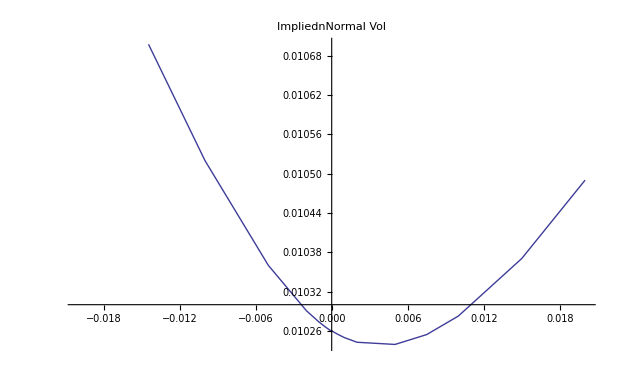
{431.235,-Graphics-}

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2=1,β2=1,Z1,Z2,τ,S,α1=1,β1=1,a=1,b=1,KList,λ1,λ2,printflag,prices,smile},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.005;ρ3=-0.5;λv3=0.35;θv3=0.05;κ3=0.2;V3=0.01;τ=5;Z1=0.1;Z2=0.2;λ1=1.1;λ2=1.01;S={0.05,0.05};printflag={1,8};
KList={-0.02,-0.015,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
prices=SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
printflag];
smile=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices[[i]]]},{i,1,Length[KList]}];
ListPlot[smile,PlotLabel->"ImpliednNormal Vol",Joined->True]
]]
```

S=(0.05
0.05) Process V1=(V1 | 0.001
λv1 | 0.15
θv1 | 0.05
κ1 | 0.2
ρ1 | -0.5) Process V2=(V2 | 0.005
λv2 | 0.15
θv2 | 0.05
κ2 | 0.2
ρ2 | -0.5) Process V3=(V3 | 0.001
λv2 | 0.35
θv3 | 0.05
κ3 | 0.2
ρ3 | -0.5) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

sum pre-initiale={0.164825,0.16399,0.163158,0.160676,0.156594,0.148631,0.126333,0.109548,0.0943514,0.0685016,0.0482509}

sum initiale={0.162426,0.161422,0.160422,0.157449,0.152585,0.14319,0.117624,0.0991831,0.0831572,0.0575205,0.0390078}

kini=10 increment initial={-0.0000574206,-0.0000572402,-0.0000570354,-0.0000562676,-0.0000545208,-0.000049531,-0.0000283867,-0.0000107556,1.86802×10^-6,0.0000117599,0.0000102772}

i=2 Kini=20. increment ={9.80499×10^-9,1.13222×10^-8,1.25018×10^-8,1.52375×10^-8,1.84381×10^-8,2.24453×10^-8,2.7518×10^-8,2.90539×10^-8,2.98274×10^-8,3.07539×10^-8,3.16791×10^-8}

raison={increment<=ϵ :          -9
9.80499 10,Null,Null,Null}

Sum finale={0.162369,0.161364,0.160365,0.157393,0.15253,0.14314,0.117595,0.0991724,0.0831591,0.0575323,0.0390181}

Fin partie positive

sum pre-initiale={0.0535774,0.0724917,0.0963675,0.125824,0.146399,0.153762,0.15754,0.159838,0.160609}

sum initiale={0.0441303,0.0620952,0.0866411,0.119497,0.143909,0.152901,0.157563,0.160414,0.161373}

kini=10 increment initial={-4.86497×10^-6,-0.0000142748,-0.0000246304,-0.0000206091,9.0773×10^-7,0.0000122753,0.0000187246,0.0000228342,0.0000242444}

raison={increment<=ϵ :          -6
4.86497 10,Null,Null,Null}

Sum finale={0.0441303,0.0620952,0.0866411,0.119497,0.143909,0.152901,0.157563,0.160414,0.161373}

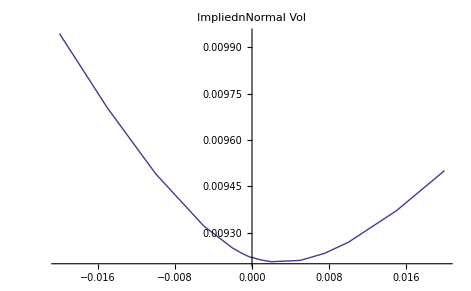
{423.359,-Graphics-}

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2=1,β2=1,Z1,Z2,τ,S,α1=1,β1=1,a=1,b=1,KList,λ1,λ2,printflag,prices,smile},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.001;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.005;ρ3=-0.5;λv3=0.35;θv3=0.05;κ3=0.2;V3=0.001;τ=5;Z1=0.1;Z2=0.2;λ1=1.1;λ2=1.01;S={0.05,0.05};printflag={1,8};
KList={-0.02,-0.015,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
prices=SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
printflag];
smile=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices[[i]]]},{i,1,Length[KList]}];
ListPlot[smile,PlotLabel->"ImpliednNormal Vol",Joined->True]
]]
```

S=(0.05
0.05) Process V1=(V1 | 0.0003
λv1 | 0.15
θv1 | 0.05
κ1 | 0.2
ρ1 | -0.5) Process V2=(V2 | 0.01
λv2 | 0.15
θv2 | 0.05
κ2 | 0.2
ρ2 | -0.5) Process V3=(V3 | 0.0003
λv2 | 0.35
θv3 | 0.05
κ3 | 0.2
ρ3 | -0.5) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

sum pre-initiale={0.168378,0.16755,0.166726,0.164273,0.160239,0.152375,0.130367,0.1138,0.0987879,0.0731861,0.0530023}

sum initiale={0.165571,0.164573,0.163581,0.160634,0.155815,0.146521,0.121279,0.103102,0.0873103,0.0619995,0.0435905}

kini=10 increment initial={-0.0000610902,-0.0000608866,-0.0000606563,-0.0000598,-0.0000578721,-0.000052444,-0.0000299145,-0.0000114192,1.77836×10^-6,0.0000122184,0.0000108397}

i=2 Kini=20. increment ={-1.02139×10^-8,-8.56293×10^-9,-7.27807×10^-9,-4.29525×10^-9,-7.97927×10^-10,3.60213×10^-9,9.27053×10^-9,1.10697×10^-8,1.20349×10^-8,1.32786×10^-8,1.45149×10^-8}

raison={increment<=ϵ :          -8
1.02139 10,Null,Null,Null}

Sum finale={0.16551,0.164512,0.16352,0.160574,0.155757,0.146468,0.121249,0.103091,0.087312,0.0620117,0.0436014}

Fin partie positive

sum pre-initiale={0.0533925,0.0720433,0.0956304,0.124821,0.145275,0.152609,0.156374,0.158665,0.159434}

sum initiale={0.0437487,0.0614184,0.0856209,0.118156,0.142444,0.151416,0.156073,0.158923,0.159882}

kini=10 increment initial={-5.11896×10^-6,-0.0000151047,-0.0000261089,-0.0000217271,1.5387×10^-6,0.0000139199,0.0000209678,0.0000254659,0.0000270105}

raison={increment<=ϵ :          -6
5.11896 10,Null,Null,Null}

Sum finale={0.0437487,0.0614184,0.0856209,0.118156,0.142444,0.151416,0.156073,0.158923,0.159882}

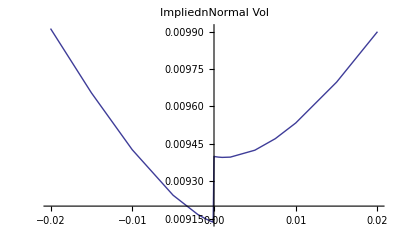
{414.609,-Graphics-}

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2=1,β2=1,Z1,Z2,τ,S,α1=1,β1=1,a=1,b=1,KList,λ1,λ2,printflag,prices,smile},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.0003;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;ρ3=-0.5;λv3=0.35;θv3=0.05;κ3=0.2;V3=0.0003;τ=5;Z1=0.1;Z2=0.2;λ1=1.1;λ2=1.01;S={0.05,0.05};printflag={1,8};
KList={-0.02,-0.015,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
prices=SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,
printflag];
smile=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices[[i]]]},{i,1,Length[KList]}];
ListPlot[smile,PlotLabel->"ImpliednNormal Vol",Joined->True]
]]
```

## Calculs des observables d'un superheston

dF=√v_1 F dW_1+√v_2 F dW_2;

dG=√v_3 G dW_3+√v_2 G  dW_2;

dv_1=λ_1(θ_1-v_1)dt+ ν_1 √v_1 dW_v1;
dv_2= λ_2(θ_2-v_2)dt+ν_2 √v_2 dW_v2;
dv_3= λ_3(θ_3-v_3)dt+ν_3 √v_3 dW_v3;
dW_1 dW_v1=ρ_1 dt;dW_2 dW_v2=ρ_2 dt;dW_3 dW_v3=ρ_3 dt;  les autres =0

### Mono Underlyings

Total Vol :

VF = V1 + V2

VG = V2 + V3

Variance de Vol

V1/VF κ1^2+V2/VF κ2^2=  κF^2

V3/VG κ3^2+V2/VG κ2^2=  κG^2

Covariance Underlying / Vol

(V1 κ1)/(VF  κF) ρ1+(V2 κ2)/(VF  κF) ρ2= ρF

(V3 κ3)/(VG  κG) ρ3+(V2 κ2)/(VG κG) ρ2= ρG

```mathematica
mais il faut raisonner en variance de vol normalisée c'est a dire diviser par
```

### Correlation

Correlation[UnderlyingF,UnderlyingG]=V2/(√(V1+V2)√(V2+V3))=V2/(√VF √VG)

donc A partir de VF, VG et ρ on reconstruit :

V2=√VF √VG ρ;
V1=VF-V2;
V3=VG-V2

### Repackaging

Observable : 
 {Volunderlying1, 
  Volunderlying2, 
  Correl12,
  ρS1,ρS2,νS1,νS2,
  VolVolBalancement, CommunCorrel,
  λ1, λ2, λ3, LTVarianceFactor1, LTVarianceFactor2, LTVarianceFactor3}

Equations :

VolVolBalancement : ξ

V2/VF κ2^2= ξ    κF^2  donc  κ2^2=  ξ   κF^2 VF/V2

V1/VF κ1^2=(1- ξ)    κF^2 donc   κ1^2=(1- ξ)    κF^2 VF/V1

V3/VG κ3^2+V2/VG κ2^2=  κG^2 donc    κ3^2= VG/V3 κG^2- V2/V3 κ2^2=VG/V3 κG^2- V2/V3 κ2^2=VG/V3 κG^2- VF/V3 ξ   κF^2

0<ξ<Min[1,VG/VF κG^2/κF^2]

CommunCorrel : ρ2

si on se donne ρ 2 ,  on  a :

ρ1= (VF  κF)/(V1 κ1)  ρF-(V2 κ2)/(V1 κ1) ρ2

et

ρ3= (VG  κG)/(V3 κ3) ρG-(V2 κ2)/(V3 κ3) ρ2

mais on doit avoir :(V1 κ1+  VF  κF  ρF)/(V2 κ2)>  ρ2  et   (V3 κ3+  VG  κG  ρG)/(V2 κ2)> ρ2

soit ρ2 <Min[1, (V1 κ1+  VF  κF  ρF)/(V2 κ2),(V3 κ3+  VG  κG  ρG)/(V2 κ2)]

de meme on doit avoir   (VF  κF)/(V1 κ1)  ρF-(V2 κ2)/(V1 κ1) ρ2<1  et  (VG  κG)/(V3 κ3) ρG-(V2 κ2)/(V3 κ3) ρ2<1

soit    ρ2> (VF  κF  ρF-V1 κ1)/(V2 κ2)  et  ρ2>(VG  κG  ρG-V3 κ3)/(V2 κ2)

soit ρ2>Max[-1,(VF  κF  ρF-V1 κ1)/(V2 κ2),(VG  κG  ρG-V3 κ3)/(V2 κ2)]

donc en resume

Max[-1,(VF  κF  ρF-V1 κ1)/(V2 κ2),(VG  κG  ρG-V3 κ3)/(V2 κ2)]<ρ2<Min[1, (V1 κ1+  VF  κF  ρF)/(V2 κ2),(V3 κ3+  VG  κG  ρG)/(V2 κ2)]

## Packaging of the Spreadoption

## Pricing packagé des options sur underlying

```mathematica
PackagedSmileBiSuperHestonUnderlyingOption1[S1_,S2_,α_,a_,KList_,T_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ1_,λ2_,λ3_,LTVarianceFactor1_,LTVarianceFactor2_,LTVarianceFactor3_,
printflag_]:=
Module[{S,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3},
V2=√VolS1 √VolS2 Correl12;V1=VolS1-V2;V3=VolS2-V2;
 κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;
θv1=V1 LTVarianceFactor1;θv2=V2 LTVarianceFactor2;θv3=V3 LTVarianceFactor3;
λv1=λ1;λv2=λ2;λv3=λ3;
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",{S1,S2} // MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λv1},{"θv1",θv1},{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"V2",V2},{"λv2",λv2},{"θv2",θv2},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λv3},{"θv3",θv3},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",T]];
Table[SuperHestonVanillaOption[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S1,KList[[i]],α,a,T],{i,1,Length[KList]}]]
```

```mathematica
PackagedSmileBiSuperHestonUnderlyingOption2[S1_,S2_,α_,a_,KList_,T_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ1_,λ2_,λ3_,LTVarianceFactor1_,LTVarianceFactor2_,LTVarianceFactor3_,
printflag_]:=
Module[{S,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3},
V2=√VolS1 √VolS2 Correl12;V1=VolS1-V2;V3=VolS2-V2;
κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;
θv1=V1 LTVarianceFactor1;θv2=V2 LTVarianceFactor2;θv3=V3 LTVarianceFactor3;
λv1=λ1;λv2=λ2;λv3=λ3;
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",{S1,S2} // MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λv1},{"θv1",θv1},{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"V2",V2},{"λv2",λv2},{"θv2",θv2},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λv3},{"θv3",θv3},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",T]];
Table[SuperHestonVanillaOption[ρ3,λv3,θv3,κ3,V3,ρ2,λv2,θv2,κ2,V2,S2,KList[[i]],α,a,T],{i,1,Length[KList]}]]
```

```mathematica
Module[{S1=0.05,S2=0.05,α1=1,a=1,KList={0.04,0.05,0.06},τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.8,ρS1=0.01,ρS2=0.05,νS1=0.3,νS2=0.4,VolVolBalancement=0.5,CommunCorrel=0.05,
λ1=0.15,λ2=0.15,λ3=0.15,LTVarianceFactor1=1.5,LTVarianceFactor2=1.5,LTVarianceFactor3=1.5,
printflag={1}},
PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,α1,a,KList,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag]]
```

S=(0.05
0.05) Process V1=(V1 | 0.002
λv1 | 0.15
θv1 | 0.003
κ1 | 0.474342
ρ1 | -0.0683772) Process V2=(V2 | 0.008
λv2 | 0.15
θv2 | 0.012
κ2 | 0.237171
ρ2 | 0.05) Process V3=(V3 | 0.002
λv2 | 0.15
θv3 | 0.003
κ3 | 0.575
ρ3 | 0.0914188) T=5

{0.0108497,0.00336706,0.00131536}

```mathematica
Module[{S1=0.05,S2=0.05,α1=1,a=1,KList={0.04,0.05,0.06},τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.8,ρS1=0.01,ρS2=0.05,νS1=0.3,νS2=0.4,VolVolBalancement=0.5,CommunCorrel=0.05,
λ1=0.15,λ2=0.15,λ3=0.15,LTVarianceFactor1=1.5,LTVarianceFactor2=1.5,LTVarianceFactor3=1.5,
printflag={1}},
PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,α1,a,KList,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag]]
```

S=(0.05
0.05) Process V1=(V1 | 0.002
λv1 | 0.15
θv1 | 0.003
κ1 | 0.474342
ρ1 | -0.0683772) Process V2=(V2 | 0.008
λv2 | 0.15
θv2 | 0.012
κ2 | 0.237171
ρ2 | 0.05) Process V3=(V3 | 0.002
λv2 | 0.15
θv3 | 0.003
κ3 | 0.575
ρ3 | 0.0914188) T=5

{0.0108283,0.00333901,0.00132528}

## Pricing packagé des spreadoption

```mathematica
PackagedSmileFourierBiSuperHestonVanillaSpreadoption[S1_,S2_,α1_,β1_,a_,b_,KList_,τ_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ1_,λ2_,λ3_,LTVarianceFactor1_,LTVarianceFactor2_,LTVarianceFactor3_,
printflag_]:=
Module[{S,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3},
S={S1,S2};
V2=√VolS1 √VolS2 Correl12;
V1=VolS1-V2;
V3=VolS2-V2;
 κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;
θv1=V1 LTVarianceFactor1;
θv2=V2 LTVarianceFactor2;
θv3=V3 LTVarianceFactor3;
λv1=λ1;λv2=λ2;λv3=λ3;
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",{S1,S2} // MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λv1},{"θv1",θv1},{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"V2",V2},{"λv2",λv2},{"θv2",θv2},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λv3},{"θv3",θv3},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",τ]];
If[printflag==9 || MemberQ[printflag,9]  ,
Print[Plot3D[SmileSymetrizedBiSuperHestonVanillaIntegrand[{S1,S2},α1,β1,a,b,{0},τ,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1.1,1.01,Z1,Z2][[1]],{Z1,-1,1},{Z2,-5,5},PlotRange->All]]];
SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,
printflag]]
```

```mathematica
Off[InterpolatingFunction::"dmval"]
```

Vol Normale Underlying1=0.00627141Vol Normale Underlying2=0.00651046

Implied Normal Correlation ATM for the spread: 0.976737

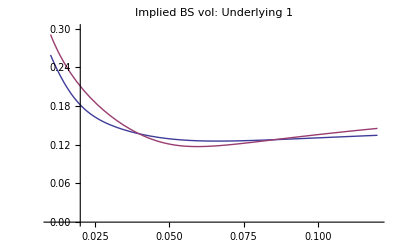
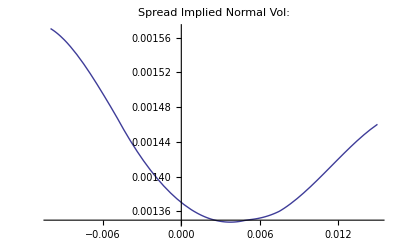
{4.656,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1,S2,α1=1,β1=1,a=1,b=1,spreadstrikes,τ=5,
VolS1=0.017,VolS2=0.017,Correl12=0.9,ρS1=-0.5,ρS2=-0.5,νS1=0.13,νS2=0.13,VolVolBalancement=0.2,CommunCorrel=-0.27,
λ1=0.15,λ2=0.15,λ3=0.15,LTVarianceFactor1=1.5,LTVarianceFactor2=1.5,LTVarianceFactor3=1.5,
printflag={0},
strikes,prices1,smile1,prices2,smile2,inter1,inter2,smileMarket1,smileMarket2,ATMimpliedCorr,
interMarket1,interMarket2,spreadprices,spreadsmile,interspread,VolNormal1,VolNormal2,spreadMarket,interspreadMarket,
tenor1="cms5",tenor2="cms10"},
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
spreadstrikes={-0.01,-0.005,-0.002,-0.001,-0.0005,0,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015};
prices1=PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
prices2=PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
smile2=Table[{strikes[[i]],ImpVolBS[S2,strikes[[i]],τ,prices2[[i]]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];inter2=Interpolation[smile2];
smileMarket1=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor1][[1]]},{i,1,Length[strikes]}];
smileMarket2=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor2][[1]]},{i,1,Length[strikes]}];
interMarket1=Interpolation[smileMarket1];interMarket2=Interpolation[smileMarket2];

VolNormal1=inter1[S1] S1;VolNormal2=inter2[S2] S2;Print["Vol Normale Underlying1=",VolNormal1,"Vol Normale Underlying2=",VolNormal2];
ATMimpliedCorr=NormalImplicitVol[VolNormal1,VolNormal2,MarketCMSSpreadOptionNormalVol[S1-S2,τ,tenor1,tenor2][[1]]];
Print["Implied Normal Correlation ATM for the spread: ",ATMimpliedCorr];
spreadMarket=Table[{spreadstrikes[[i]],MarketCMSSpreadOptionNormalVol[spreadstrikes[[i]],τ,tenor1,tenor2][[1]]},{i,1,Length[spreadstrikes]}];
interspreadMarket=Interpolation[spreadMarket];
{Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{interspreadMarket[x]},{x,spreadstrikes[[1]],Last[spreadstrikes]},PlotLabel->"Spread Implied Normal Vol:",
PlotLegend->{"Market"},LegendPosition->{1,0},PlotRange->All]}]]
```

-Graphics3D-

S=(0.0481839
0.0500812) Process V1=(V1 | 0.00034
λv1 | 0.15
θv1 | 0.00051
κ1 | 0.581378
ρ1 | 0.41108) Process V2=(V2 | 0.01666
λv2 | 0.15
θv2 | 0.02499
κ2 | 0.10172
ρ2 | -0.7) Process V3=(V3 | 0.00034
λv2 | 0.15
θv3 | 0.00051
κ3 | 0.338
ρ3 | 0.707079) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

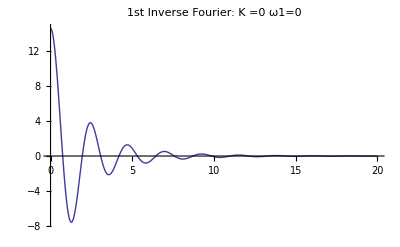
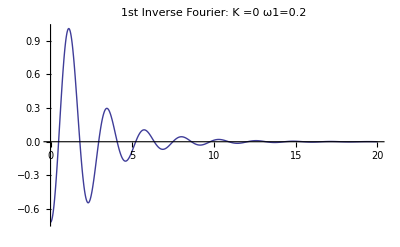
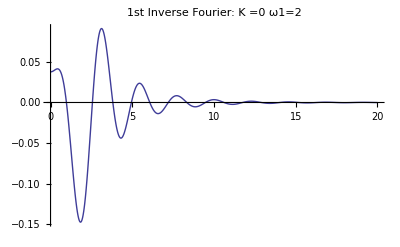

Fin partie positive

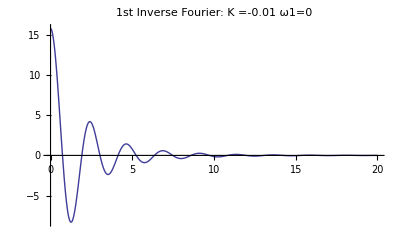
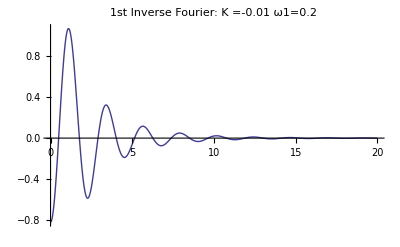
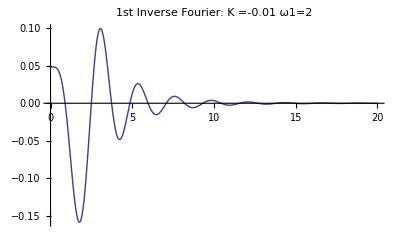

Vol Normale Underlying1=0.00607352Vol Normale Underlying2=0.00631746

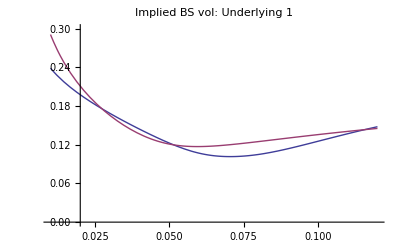
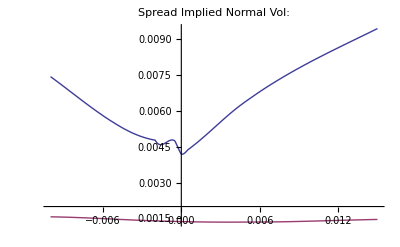
{479.14,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1,S2,α1=1,β1=1,a=1,b=1,spreadstrikes,τ=5,
VolS1=0.017,VolS2=0.017,Correl12=0.98,ρS1=-0.5,ρS2=-0.5,νS1=0.13,νS2=0.13,VolVolBalancement=0.6,CommunCorrel=-0.7,
λ1=0.15,λ2=0.15,λ3=0.15,LTVarianceFactor1=1.5,LTVarianceFactor2=1.5,LTVarianceFactor3=1.5,
printflag={0},
strikes,prices1,smile1,prices2,smile2,inter1,inter2,smileMarket1,smileMarket2,
interMarket1,interMarket2,spreadprices,spreadsmile,interspread,VolNormal1,VolNormal2,spreadMarket,interspreadMarket,
tenor1="cms5",tenor2="cms10"},
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
spreadstrikes={-0.01,-0.005,-0.002,-0.001,-0.0005,0,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015};
prices1=PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
prices2=PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
smile2=Table[{strikes[[i]],ImpVolBS[S2,strikes[[i]],τ,prices2[[i]]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];inter2=Interpolation[smile2];
smileMarket1=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor1][[1]]},{i,1,Length[strikes]}];
smileMarket2=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor2][[1]]},{i,1,Length[strikes]}];
interMarket1=Interpolation[smileMarket1];interMarket2=Interpolation[smileMarket2];
spreadprices=PackagedSmileFourierBiSuperHestonVanillaSpreadoption[S1,S2,α1,β1,a,b,spreadstrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,νS1,νS2,VolVolBalancement,CommunCorrel,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
{1,4,9}];
spreadsmile=Table[{spreadstrikes[[i]],NormalImplicitVol[S1-S2,spreadstrikes[[i]],τ,spreadprices[[i]]]},{i,1,Length[spreadstrikes]}];
interspread=Interpolation[spreadsmile];
VolNormal1=inter1[S1] S1;VolNormal2=inter2[S2] S2;Print["Vol Normale Underlying1=",VolNormal1,"Vol Normale Underlying2=",VolNormal2];
spreadMarket=Table[{spreadstrikes[[i]],MarketCMSSpreadOptionNormalVol[spreadstrikes[[i]],τ,tenor1,tenor2][[1]]},{i,1,Length[spreadstrikes]}];
interspreadMarket=Interpolation[spreadMarket];
{Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{interspread[x],interspreadMarket[x]},{x,spreadstrikes[[1]],Last[spreadstrikes]},PlotLabel->"Spread Implied Normal Vol:",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->All]}]]
```

## Determinations des moments liés au normal Heston et au BiSuperHeston

```mathematica
NormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
ⅇ^(A+B V)]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A+B V]
```

```mathematica
D2=D[LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω,τ],{ω,2}];
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[1/ⅈ^2 D2/. ω->0]];
```

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

```mathematica
Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.01,ω=0,τ=30},
{
D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]}
]
```

{1.00222}

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

```mathematica
BiSuperLogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,Z1_,Z2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,ζ2,ψp2 ,ψm2,A2,ζ3,ψp3 ,ψm3,A3,c},
ζ1=√((λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1));
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
ζ2=√((λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2));
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
ζ3=√((λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2));
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
```

```mathematica
LogBiSuperLogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,Z1_,Z2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,ζ2,ψp2 ,ψm2,A2,ζ3,ψp3 ,ψm3,A3,c},
ζ1=√((λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1));
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
ζ2=√((λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2));
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
ζ3=√((λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2));
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
c+A1 V1+A2 V2+A3 V3]
```

```mathematica
D1X=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1];
D1XBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[1/ⅈ D1X /.{Z1->0,Z2->0}]];
```

```mathematica
D1Y=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z2];
D1YBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[1/ⅈ D1Y/.{Z1->0,Z2->0}]];
```

```mathematica
D2XX=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z1,2}];
D2XXBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[1/ⅈ^2 D2XX/.{Z1->0,Z2->0}]];
```

```mathematica
D2YY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z2,2}];
D2YYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[1/ⅈ^2 D2YY/.{Z1->0,Z2->0}]];
```

```mathematica
D2XY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1,Z2];
D2XYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[1/ⅈ^2 D2XY/.{Z1->0,Z2->0}]];
```

## Projection du generateur de Bisuperheston sur les generateurs Normalheston

le generateur

dF=√v_1 F dW_1+α2 √v_2 F dW_2;

dG=√v_3 G dW_3+β2 √v_2 G  dW_2;

dv_1=λ_1(θ_1-v_1)dt+ ν_1 √v_1 dW_v1;
dv_2= λ_2(θ_2-v_2)dt+ν_2 √v_2 dW_v2;
dv_3= λ_3(θ_3-v_3)dt+ν_3 √v_3 dW_v3;
dW_1 dW_v1=ρ_1 dt;dW_2 dW_v2=ρ_2 dt;dW_3 dW_v3=ρ_3 dt;  les autres =0

S = F - G

dS=√v_2( α2 F-β2 G) dW_2+√v_1 F dW_1-√v_3 G dW_3

Le processus de vol est donc donné par

V_S=v_2(α2 F-β2 G)^2+v_1 F^2+v_3 G^2

## Derivation Symboliques

### 1) BiSuperheston

```mathematica
Cov={
{1,0,0,ρ1,0,0},
{0,1,0,0,ρ2,0},
{0,0,1,0,0,ρ3},
{ρ1,0,0,1,0,0},
{0,ρ2,0,0,1,0},
{0,0,ρ3,0,0,1}
};
```

```mathematica
Diff[x_]:=D[x,S1]{√V1 S1,α2 √V2 S1,0,0,0,0}+
D[x,S2]{0,β2 √V2 S2,√V3 S2,0,0,0}+
D[x,V1]{0,0,0,κ1 √V1,0,0}+
D[x,V2]{0,0,0,0,κ2 √V2,0}+
D[x,V3]{0,0,0,0,0,κ3 √V3}
```

```mathematica
VS=Simplify[Diff[S1-S2].(Cov.Diff[S1-S2])]
```

S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2

```mathematica
VarVS=Simplify[Diff[VS].(Cov.Diff[VS])]
```

S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3))

```mathematica
CoVarSVS=Simplify[Diff[VS].(Cov.Diff[S1-S2])]
```

2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3

Que l' on identifie avec les meme calculs fait avec normal heston :

### 2) Normal Heston

```mathematica
CovNH={
{1,ρ},
{ρ,1}
};
```

```mathematica
DiffNH[x_]:=D[x,S]{√v,0}+
D[x,v]{0,ν √v }
```

```mathematica
VSNH=Simplify[DiffNH[S].(CovNH.DiffNH[S])]
```

v

```mathematica
VarVSNH=Simplify[DiffNH[VSNH].(CovNH.DiffNH[VSNH])]
```

v ν^2

```mathematica
CoVarSVS=Simplify[DiffNH[VSNH].(CovNH.DiffNH[S])]
```

v ν ρ

ce qui permet d' extraire les parametres utiles :

v = VSNH

ν^2=VarVSNH/v=VarVSNH/VSNH

ρ=CoVarSVS/(v ν)=CoVarSVS/VarVSNH

## Pricing rapide de spreadoption dans le bisuperheston

```mathematica
SmileBiSuperHestonVanillaSpreadOption[S1_,S2_, ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,SpreadStrikes_,τ_,printflag_]:=Module[{Z1,Z2,VarExpX,VarExpY,VarRealSpead,ρprojeté,νprojeté,
μX,μY,μXX,μYY,μXY,μXXX,μXXY,μXYY,μYYY,μXXXX,μXXXY,μXXYY,μXYYY,μYYYY,
μ1,μ2,μ3,μ4,V0Generateur,κS,ρS,λS,LTFactorS,TrueIniVarSpread,x,prices,logcorrelT,ρmodel,VarVS,CoVarSVS,VS},
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]}};
If[printflag==1 || MemberQ[printflag,1] ,Print["moments=",{{μX,μY},{μXX,μYY,μXY}}]];
logcorrelT=μXY/√(μXX μYY);
If[printflag==1 || MemberQ[printflag,1] ,Print["logcorrelT=",logcorrelT]];
VarVS=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
CoVarSVS=2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3;
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;
ρprojeté=CoVarSVS/VarVS;νprojeté=√(VarVS/VS);
VarExpX=LogHestonNormalVariance[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,√α2 V2,S1,τ];
VarExpY=LogHestonNormalVariance[ρ3,λv3,θv3,κ3,V3,ρ2,λv2,θv2,κ2,√β2 V2,S2,τ];
VarRealSpead=VarExpX+VarExpY-2logcorrelT √(VarExpX VarExpY);
If[printflag==1 || MemberQ[printflag,1] ,Print["VarRealSpead (Goal)=",VarRealSpead]];

LTFactorS=1.5;
λS=0.15;

TrueIniVarSpread=(ⅇ^(λS τ) VarRealSpead λS)/(-1+LTFactorS+ⅇ^(λS τ) (1+LTFactorS (-1+λS τ)));
If[printflag==1 || MemberQ[printflag,1] ,Print["TrueIniVarSpread=",TrueIniVarSpread]];

If[printflag==1 || MemberQ[printflag,1] ,Print["TrueIniVarSpread=",TrueIniVarSpread]];
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",S1-S2},{"V0",TrueIniVarSpread},{"θ",LTFactorS TrueIniVarSpread},{"λv",λS},{"ρ",ρS},{"ν",κS}} //MatrixForm]];
prices=HestonNormalCallTrace[ρS,λS,LTFactorS TrueIniVarSpread,κS,TrueIniVarSpread,S1-S2,SpreadStrikes,τ];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
prices
]
```

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,SpreadStrikes},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.2;V1=0.01;
ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.2;V2=0.01;
ρ3=-0.5;λv3=0.15;θv3=0.05;κ3=0.2;V3=0.01;
τ=10;S1=0.05;S2=0.045;SpreadStrikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015};
SmileBiSuperHestonVanillaSpreadOption[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,SpreadStrikes,τ,0]]
```

L=260.892 κ1=4.97738 S01=1.30446 k1={-3.91337,-2.60892,-1.30446,-0.260892,0,0.260892,1.30446,2.60892,3.91337}

{0.014555,0.0117029,0.00822231,0.00524888,0.0045101,0.00378556,0.00134567,0.000318421,0.000106645}

### Comparaison pricing rapide / pricing fourier

S=(0.05
0.05) Process V1=(V1 | 0.01
λv1 | 0.15
θv1 | 0.05
κ1 | 0.02
ρ1 | -0.5) Process V2=(V2 | 0.01
λv2 | 0.15
θv2 | 0.05
κ2 | 0.02
ρ2 | -0.5) Process V3=(V3 | 0.01
λv2 | 0.35
θv3 | 0.05
κ3 | 0.02
ρ3 | -0.5) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ]=0.996147+0.024075 ⅈ

integrand(0.1,0.1)={5.91995,5.91762,5.91564,5.91036,5.9026,5.88889,5.85422,5.8291,5.80604,5.76408,5.72603}

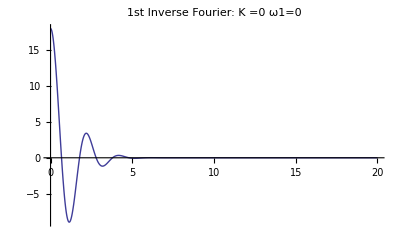
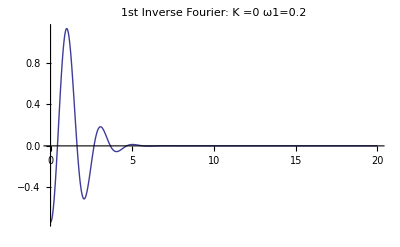
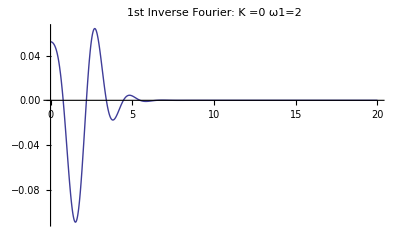

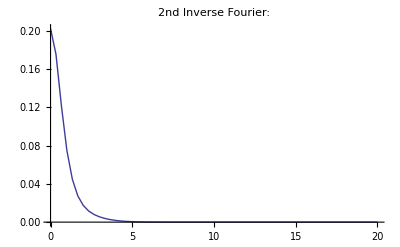

sum pre-initiale={0.192958,0.192108,0.191264,0.188753,0.184628,0.176583,0.154032,0.137008,0.121547,0.0950743,0.0739756}

sum initiale={0.20772,0.206707,0.205701,0.202712,0.197809,0.188283,0.161887,0.142317,0.124851,0.0956979,0.0732012}

k={10,15.}  increment initial={-1.75218×10^-9,-1.76065×10^-9,-1.76759×10^-9,-1.78241×10^-9,-1.79373×10^-9,-1.78617×10^-9,-1.6549×10^-9,-1.50017×10^-9,-1.33642×10^-9,-1.01914×10^-9,-7.33558×10^-10}

raison={increment<=ϵ :          -9
1.75218 10,Null,Null,Null}

Sum finale={0.20772,0.206707,0.205701,0.202712,0.197809,0.188283,0.161887,0.142317,0.124851,0.0956979,0.0732012}

Fin partie positive

BiSuperHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ]=0.996147+0.024075 ⅈ

integrand(0.1,0.1)={5.51228,5.5487,5.58886,5.63496,5.66812,5.68122,5.68864,5.69369,5.69558}

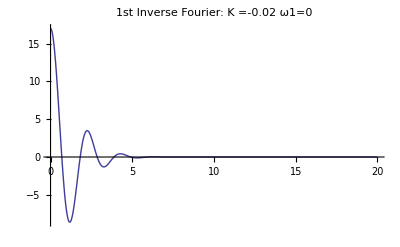
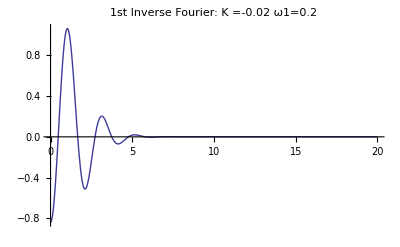
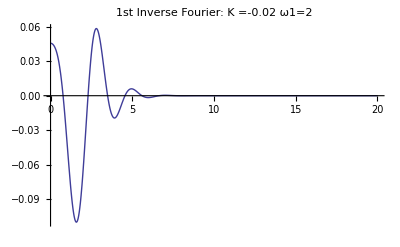

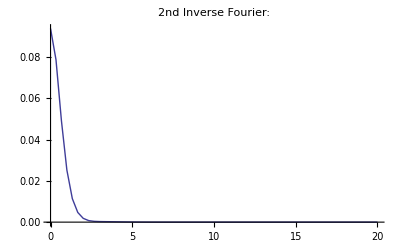

sum pre-initiale={0.0723486,0.0921803,0.117028,0.14766,0.169058,0.17671,0.180635,0.183022,0.183822}

sum initiale={0.0734041,0.0946332,0.121879,0.156451,0.181216,0.190187,0.19481,0.197628,0.198575}

k={10,15.}  increment initial={-1.57704×10^-9,-1.98462×10^-9,-2.42173×10^-9,-2.81284×10^-9,-2.91554×10^-9,-2.89179×10^-9,-2.86084×10^-9,-2.83413×10^-9,-2.82365×10^-9}

raison={increment<=ϵ :          -9
1.57704 10,Null,Null,Null}

Sum finale={0.0734041,0.0946332,0.121879,0.156451,0.181216,0.190187,0.19481,0.197628,0.198575}

moments={{0.109298,0.132436},{0.222399,0.268874,0.1112}}

VarSpread (Goal)=0.000134437

V0Generateur=0.00005

VarSpread (initial)  obtenu dans le normal Heston a partir du V0Generateur =0.000287061

TrueIniVarSpread=0.0000234161

Normal Heston Parameters=(S0 | 0.
V0 | 0.0000234161
θ | 0.0000351241
λv | 0.15
ρ | 0.
ν | 0.002)

L=206.654 κ1=0.413307 S01=0. k1={-4.13307,-3.09981,-2.06654,-1.03327,-0.413307,-0.206654,-0.103327,-0.0413307,-0.0206654,0,0.0206654,0.0413307,0.103327,0.206654,0.413307,1.03327,1.5499,2.06654,3.09981,4.13307}

prices={0.0202321,0.0155575,0.0112347,0.00749212,0.00561949,0.00506528,0.00480169,0.00464788,0.00459734,0.00454716,0.00449734,0.00444788,0.00430169,0.00406528,0.00361949,0.00249212,0.00177573,0.00123471,0.000557536,0.000232092}

smile fourier={{-0.02,0.0122513},{-0.015,0.0119463},{-0.01,0.0116808},{-0.005,0.0114702},{-0.002,0.0113772},{-0.001,0.0113525},{-0.0005,0.0113414},{-0.0002,0.0113351},{-0.0001,0.0113331},{0,0.0117965},{0.0001,0.0117949},{0.0002,0.0117936},{0.0005,0.0117902},{0.001,0.0117856},{0.002,0.0117798},{0.005,0.0117846},{0.0075,0.011813},{0.01,0.0118622},{0.015,0.012017},{0.02,0.0122363}}

smile rapide={{-0.02,0.00534019},{-0.015,0.0052431},{-0.01,0.00516566},{-0.005,0.00511504},{-0.002,0.00510021},{-0.001,0.00509807},{-0.0005,0.00509753},{-0.0002,0.00509738},{-0.0001,0.00509736},{0,0.00509735},{0.0001,0.00509736},{0.0002,0.00509738},{0.0005,0.00509753},{0.001,0.00509807},{0.002,0.00510021},{0.005,0.00511504},{0.0075,0.00513656},{0.01,0.00516566},{0.015,0.0052431},{0.02,0.00534019}}

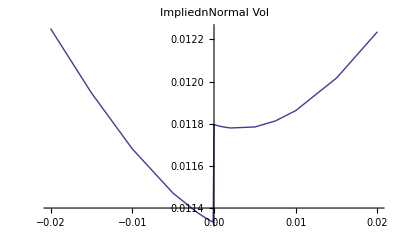
{125.16,-Graphics-}

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S,α1=1,β1=1,a=1,b=1,KList,λ1,λ2,printflag,prices,smile,prices2,smile2},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.02;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.02;V2=0.01;ρ3=-0.5;λv3=0.35;θv3=0.05;κ3=0.02;V3=0.01;τ=5;Z1=0.1;Z2=0.2;λ1=1.1;λ2=1.01;S={0.05,0.05};printflag={1,2,4,6,8};
KList={-0.02,-0.015,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
prices=SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,
printflag];
prices2=SmileBiSuperHestonVanillaSpreadOption[S[[1]],S[[2]], ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,KList,τ,1];

smile=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices[[i]]]},{i,1,Length[KList]}];
smile2=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices2[[i]]]},{i,1,Length[KList]}];

Print["smile fourier=",smile];Print["smile rapide=",smile2];
g1=ListPlot[smile,PlotLabel->"ImpliednNormal Vol",Joined->True];
g2=ListPlot[smile2,PlotLabel->"ImpliednNormal Vol",Joined->True];
Show[g1,g2]
]]
```

S=(0.05
0.05) Process V1=(V1 | 0.01
λv1 | 0.15
θv1 | 0.05
κ1 | 0.02
ρ1 | -0.5) Process V2=(V2 | 0.01
λv2 | 0.15
θv2 | 0.05
κ2 | 0.02
ρ2 | -0.5) Process V3=(V3 | 0.01
λv2 | 0.35
θv3 | 0.05
κ3 | 0.02
ρ3 | -0.5) T=5

Inner Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5
StoppingLevel | 1.×10^-6
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
ExplosionMonitoringStartAbcisse | 20
ExplosionMonitoringMaxLevel | 2
lambda1 | 1.1
lambda2 | 1.01)Outer Integration(LegendreNbMain | 50
LegendreNbIncrement | 20
IncrementNbMax | 10
InitialTailFlag | 1
InitialTailLegendreNb | 50
PeriodMain | 10
PeriodnIncrement | 5.
StoppingLevel | 0.00001
AbcisseMaxValue | 100
InitialTailUpperLimit | 0.5
GrowingControlStartAbcisse | 2
GrowingControlMaxFactor | 0.1)

sum pre-initiale={0.192958,0.192108,0.191264,0.188753,0.184628,0.176583,0.154032,0.137008,0.121547,0.0950743,0.0739756}

sum initiale={0.20772,0.206707,0.205701,0.202712,0.197809,0.188283,0.161887,0.142317,0.124851,0.0956979,0.0732012}

k={10,15.}  increment initial={-1.75218×10^-9,-1.76065×10^-9,-1.76759×10^-9,-1.78241×10^-9,-1.79373×10^-9,-1.78617×10^-9,-1.6549×10^-9,-1.50017×10^-9,-1.33642×10^-9,-1.01914×10^-9,-7.33558×10^-10}

raison={increment<=ϵ :          -9
1.75218 10,Null,Null,Null}

Sum finale={0.20772,0.206707,0.205701,0.202712,0.197809,0.188283,0.161887,0.142317,0.124851,0.0956979,0.0732012}

Fin partie positive

sum pre-initiale={0.0723486,0.0921803,0.117028,0.14766,0.169058,0.17671,0.180635,0.183022,0.183822}

sum initiale={0.0734041,0.0946332,0.121879,0.156451,0.181216,0.190187,0.19481,0.197628,0.198575}

k={10,15.}  increment initial={-1.57704×10^-9,-1.98462×10^-9,-2.42173×10^-9,-2.81284×10^-9,-2.91554×10^-9,-2.89179×10^-9,-2.86084×10^-9,-2.83413×10^-9,-2.82365×10^-9}

raison={increment<=ϵ :          -9
1.57704 10,Null,Null,Null}

Sum finale={0.0734041,0.0946332,0.121879,0.156451,0.181216,0.190187,0.19481,0.197628,0.198575}

moments={{0.109298,0.132436},{0.222399,0.268874,0.1112}}

VarSpread (Goal)=0.000134437

V0Generateur=0.00005

VarSpread (initial)  obtenu dans le normal Heston a partir du V0Generateur =0.000287061

TrueIniVarSpread=0.0001

Normal Heston Parameters=(S0 | 0.
V0 | 0.0001
θ | 0.00015
λv | 0.15
ρ | 0.
ν | 0.002)

L=100. κ1=0.2 S01=0. k1={-2.,-1.5,-1.,-0.5,-0.2,-0.1,-0.05,-0.02,-0.01,0,0.01,0.02,0.05,0.1,0.2,0.5,0.75,1.,1.5,2.}

prices={0.0227002,0.0188541,0.0153504,0.0122302,0.010554,0.0100287,0.00977238,0.00962061,0.00957036,0.00952027,0.00947036,0.00942061,0.00927238,0.0090287,0.00855396,0.00723017,0.00624031,0.00535043,0.00385411,0.00270024}

smile fourier={{-0.02,0.0122513},{-0.015,0.0119463},{-0.01,0.0116808},{-0.005,0.0114702},{-0.002,0.0113772},{-0.001,0.0113525},{-0.0005,0.0113414},{-0.0002,0.0113351},{-0.0001,0.0113331},{0,0.0117965},{0.0001,0.0117949},{0.0002,0.0117936},{0.0005,0.0117902},{0.001,0.0117856},{0.002,0.0117798},{0.005,0.0117846},{0.0075,0.011813},{0.01,0.0118622},{0.015,0.012017},{0.02,0.0122363}}

smile rapide={{-0.02,0.0107028},{-0.015,0.0106895},{-0.01,0.0106799},{-0.005,0.0106741},{-0.002,0.0106725},{-0.001,0.0106723},{-0.0005,0.0106722},{-0.0002,0.0106722},{-0.0001,0.0106722},{0,0.0106722},{0.0001,0.0106722},{0.0002,0.0106722},{0.0005,0.0106722},{0.001,0.0106723},{0.002,0.0106725},{0.005,0.0106741},{0.0075,0.0106766},{0.01,0.0106799},{0.015,0.0106895},{0.02,0.0107028}}

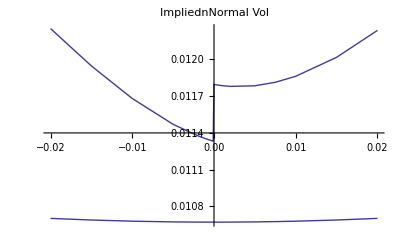
{114.473,-Graphics-}

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S,α1=1,β1=1,a=1,b=1,KList,λ1,λ2,printflag,prices,smile,prices2,smile2},
ρ1=-0.5;λv1=0.15;θv1=0.05;κ1=0.02;V1=0.01;ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.02;V2=0.01;ρ3=-0.5;λv3=0.35;θv3=0.05;κ3=0.02;V3=0.01;τ=5;Z1=0.1;Z2=0.2;λ1=1.1;λ2=1.01;S={0.05,0.05};printflag={1,8};
KList={-0.02,-0.015,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
prices=SmileBiSuperHestonVanillaSpreadotion[S,α1,β1,a,b,KList,τ,
ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,
printflag];
prices2=SmileBiSuperHestonVanillaSpreadOption[S[[1]],S[[2]], ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,KList,τ,1];

smile=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices[[i]]]},{i,1,Length[KList]}];
smile2=Table[{KList[[i]],NormalImplicitVol[S[[1]]-S[[2]],KList[[i]],τ,prices2[[i]]]},{i,1,Length[KList]}];

Print["smile fourier=",smile];Print["smile rapide=",smile2];
g1=ListPlot[smile,PlotLabel->"ImpliednNormal Vol",Joined->True];
g2=ListPlot[smile2,PlotLabel->"ImpliednNormal Vol",Joined->True];
Show[g1,g2,PlotRange->All]
]]
```

## Pricing rapide packagé des spreadoption

```mathematica
PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1_,S2_,SpreadStrikes_,τ_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ1_,λ2_,λ3_,LTVarianceFactor1_,LTVarianceFactor2_,LTVarianceFactor3_,
printflag_]:=
Module[{S,ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3},
S={S1,S2};
V2=√VolS1 √VolS2 Correl12;
V1=VolS1-V2;
V3=VolS2-V2;
κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;
θv1=V1 LTVarianceFactor1;
θv2=V2 LTVarianceFactor2;
θv3=V3 LTVarianceFactor3;
λv1=λ1;λv2=λ2;λv3=λ3;
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",{S1,S2} // MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λv1},{"θv1",θv1},{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"V2",V2},{"λv2",λv2},{"θv2",θv2},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λv3},{"θv3",θv3},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",τ]];
SmileBiSuperHestonVanillaSpreadOption[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,SpreadStrikes,τ,printflag]]
```

S=(0.0481839
0.0500812) Process V1=(V1 | 0.00051275
λv1 | 0.15
θv1 | 0.000769125
κ1 | 0.0039
ρ1 | -0.8) Process V2=(V2 | 0.0169873
λv2 | 0.15
θv2 | 0.0254809
κ2 | 0.17
ρ2 | -0.5) Process V3=(V3 | 0.00051275
λv2 | 0.15
θv3 | 0.000769125
κ3 | 0.0047
ρ3 | -0.02) T=5

moments={{0.0502357,0.0502357},{0.119626,0.119609,0.116665}}

VarSpread (Approx of the goal)=2.85134×10^-6

logcorrelT=0.975314 / ρinitial=0.9707

VarRealSpead (Goal)=0.0000100553

V0Generateur=2.53763×10^-6

VarSpread (initial)  obtenu dans le normal Heston a partir du V0Generateur =0.0000145691

TrueIniVarSpread=1.75142×10^-6

Normal Heston Parameters=(S0 | -0.00189728
V0 | 1.75142×10^-6
θ | 2.62713×10^-6
λv | 0.15
ρ | -0.311113
ν | 0.000425539)

L=755.623 κa=0.321547 S0a=-1.43363 ka={-7.55623,-3.77811,-1.51125,-0.755623,-0.377811,0,0.377811,0.755623,1.51125,3.77811,5.66717,7.55623,11.3343}

prices={0.00811677,0.00340628,0.00130554,0.000841075,0.000657051,0.000503564,0.00037838,0.00027862,0.000142032,0.0000116179,8.853×10^-7,4.75217×10^-8,6.40874×10^-11}

Vol Normale Underlying1=0.00572849Vol Normale Underlying2=0.00595186

spreadMarket={{-0.01,0.00157041},{-0.005,0.00147033},{-0.002,0.00140073},{-0.001,0.00138393},{-0.0005,0.00137673},{0,0.00137033},{0.0005,0.00136471},{0.001,0.0013599},{0.002,0.00135266},{0.005,0.00135025},{0.0075,0.00136025},{0.01,0.00139025},{0.015,0.00146025}}

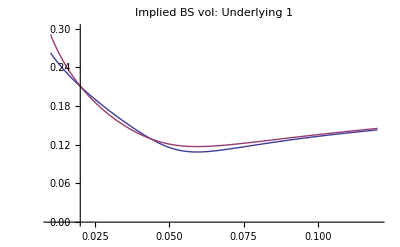
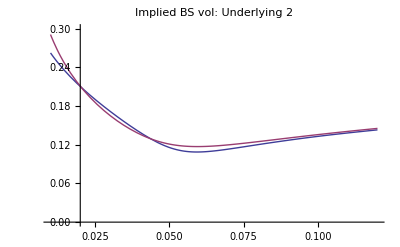
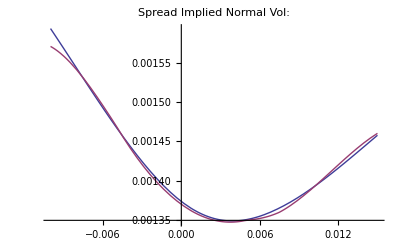
{5.156,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1,S2,α1=1,β1=1,a=1,b=1,spreadstrikes,τ=5,
VolS1=0.0175,VolS2=0.0175,Correl12=0.9707,ρS1=-0.8,ρS2=-0.5,ρS3=-0.02,κS1=0.0039,κS2=0.17,κS3=0.0047,
λ1=0.15,λ2=0.15,λ3=0.15,LTVarianceFactor1=1.5,LTVarianceFactor2=1.5,LTVarianceFactor3=1.5,
printflag={0},
strikes,prices1,smile1,prices2,smile2,inter1,inter2,smileMarket1,smileMarket2,
interMarket1,interMarket2,spreadprices,spreadsmile,interspread,VolNormal1,VolNormal2,spreadMarket,interspreadMarket,
tenor1="cms5",tenor2="cms10"},
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
spreadstrikes={-0.01,-0.005,-0.002,-0.001,-0.0005,0,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015};
prices1=PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
prices2=PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,α1,a,strikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
printflag];
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices1[[i]]]},{i,1,Length[strikes]}];
smile2=Table[{strikes[[i]],ImpVolBS[S2,strikes[[i]],τ,prices2[[i]]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1];inter2=Interpolation[smile2];
smileMarket1=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor1][[1]]},{i,1,Length[strikes]}];
smileMarket2=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor2][[1]]},{i,1,Length[strikes]}];
interMarket1=Interpolation[smileMarket1];interMarket2=Interpolation[smileMarket2];
spreadprices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,spreadstrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ1,λ2,λ3,LTVarianceFactor1,LTVarianceFactor2,LTVarianceFactor3,
{1,4,9}];
spreadsmile=Table[{spreadstrikes[[i]],NormalImplicitVol[S1-S2,spreadstrikes[[i]],τ,spreadprices[[i]]]},{i,1,Length[spreadstrikes]}];
interspread=Interpolation[spreadsmile];
VolNormal1=inter1[S1] S1;VolNormal2=inter2[S2] S2;Print["Vol Normale Underlying1=",VolNormal1,"Vol Normale Underlying2=",VolNormal2];
spreadMarket=Table[{spreadstrikes[[i]],MarketCMSSpreadOptionNormalVol[spreadstrikes[[i]],τ,tenor1,tenor2][[1]]},{i,1,Length[spreadstrikes]}];
interspreadMarket=Interpolation[spreadMarket];
Print["spreadMarket=",spreadMarket];
{Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol: Underlying 2",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{interspread[x],interspreadMarket[x]},{x,spreadstrikes[[1]],Last[spreadstrikes]},PlotLabel->"Spread Implied Normal Vol:",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->All]}]]
```